## simulation

### ϵ=1.0 for revcross

```mathematica
rhos={0.923333,2.5155};
temperatures={{0.1,0.05,0.01,0.0025,0.0022,0.001,0.0007,0.0003,0.0002,0.00009},{0.15,0.09,0.08,0.07,0.065,0.06}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/rho0.923333/dynamics/Fs_T0.00100000_rho0.923333_wait100000_k7.0.csv","CSV"];
```

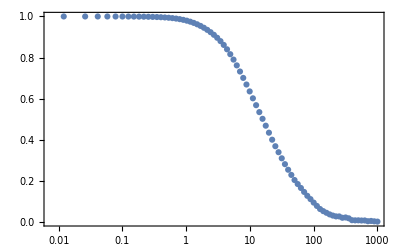

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

```mathematica
fsks=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/rho","/dynamics/Fs_T","_rho","_wait","_k8.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],100000*(wt-1)},{6,8,6,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/rho0.923333/dynamics/Fs_T0.05000000_rho0.923333_wait600000_k8.0.csv not found during Import.

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/rho0.923333/dynamics/Fs_T0.05000000_rho0.923333_wait700000_k8.0.csv not found during Import.

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/rho0.923333/dynamics/Fs_T0.05000000_rho0.923333_wait800000_k8.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

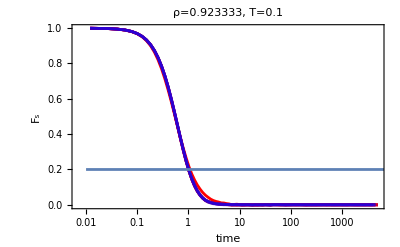
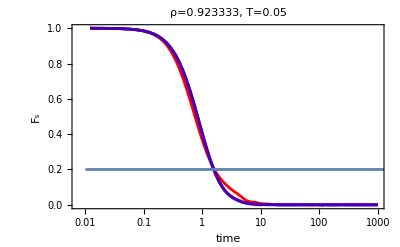
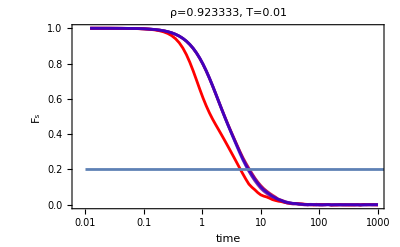
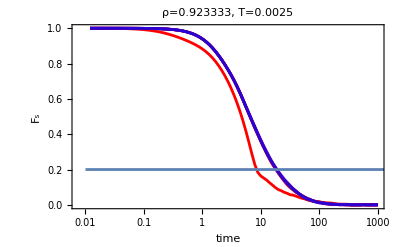
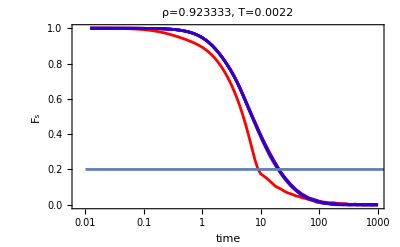
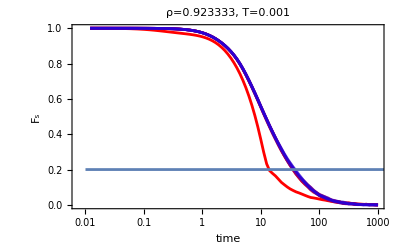
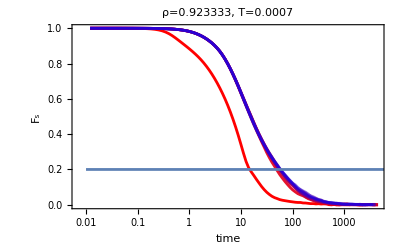
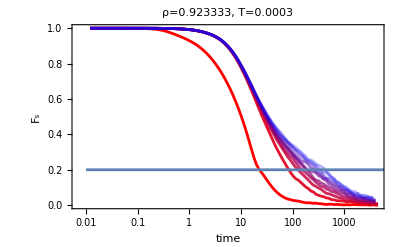

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"ρ="<>ToString[rhos[[rho]]]<>", T="<>ToString[AccountingForm[temperatures[[rho,T]]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}]
```

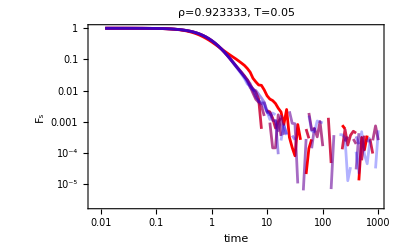
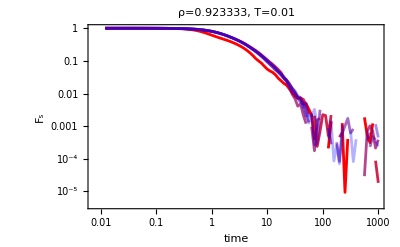
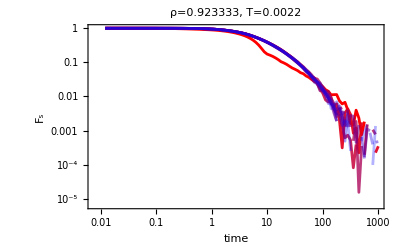

```mathematica
fsep1LogPlot=Table[Table[Show[ListLogLogPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"ρ="<>ToString[rhos[[rho]]]<>", T="<>ToString[AccountingForm[temperatures[[rho,T]]]],FrameLabel->{"time","F_s"}]],{T,{2,3,5}}],{rho,1}]
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fsep1LogPlot.jpeg",Grid[Partition[fsep1LogPlot[[1]],3]],ImageResolution->300];
```

```mathematica
tauAlpha={{1,1.8,7,18,20,37,56}};
```

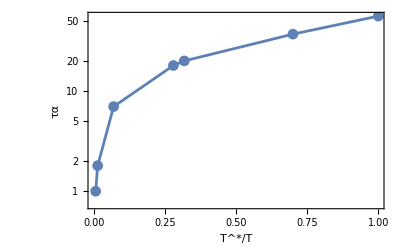

```mathematica
tauAlphaEp1Plot=Table[ListLogPlot[Table[{temperatures[[rho,Length[tauAlpha[[rho]]]]]/temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T^*/T","τα"},Joined->True],{rho,1}]
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon1.jpeg",tauAlphaEp1Plot[[1]],ImageResolution->200];
```

```mathematica
N[0.54*0.9]
```

0.486

```mathematica
Table[0.48/i/10,{i,6,9}]
```

{0.008,0.00685714,0.006,0.00533333}

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon1.jpeg",Grid[Partition[fsksPlot[[1,;;9]],3]],ImageResolution->300];
```

### ϵ=100.0kT for revcross

```mathematica
rhos={0.923333};
temperatures={{0.1,0.05,0.025,0.01,0.005,0.0025,0.001,0.0007,0.0003,0.0002}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/WCAcut0.9RevEp100/rho0.923333/dynamics/Fs_T0.00100000_rho0.923333_wait100000_k7.0.csv","CSV"];
```

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

-Graphics-

```mathematica
fsks=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/RevEp100kT/rho","/dynamics/Fs_T","_rho","_wait","_k8.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],100000*(wt-1)},{6,8,6,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/RevEp100kT/rho0.923333/dynamics/Fs_T0.10000000_rho0.923333_wait700000_k8.0.csv not found during Import.

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/RevEp100kT/rho0.923333/dynamics/Fs_T0.10000000_rho0.923333_wait800000_k8.0.csv not found during Import.

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/RevEp100kT/rho0.923333/dynamics/Fs_T0.10000000_rho0.923333_wait900000_k8.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
fsks[[1,2,3]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999771307902312612},{0.0260000000000000023,0.998927903012059804},{0.0410000000000000017,0.997341261180982541},{0.0580000000000000029,0.994703746140828127},{0.0779999999999999999,0.9904918971800174},{0.100000000000000006,0.984533957042731722},{0.123999999999999999,0.976545394256684518},{0.150999999999999995,0.965841636711015306},{0.181999999999999995,0.951520876475550836},{0.215999999999999998,0.933608209468088979},{0.255000000000000004,0.91063777198470941},{0.297999999999999987,0.882846380994267155},{0.347000000000000031,0.848717100125015445},{0.401000000000000023,0.808974891277051134},{0.462000000000000022,0.762593356061524674},{0.531000000000000028,0.709524214988034307},{0.607999999999999985,0.651153630910284997},{0.694000000000000061,0.588534881311457814},{0.791000000000000036,0.522660708122160367},{0.900000000000000022,0.455888949812410682},{1.02200000000000002,0.390465917138967278},{1.15900000000000003,0.327732678865483629},{1.31299999999999995,0.269804930866816228},{1.4850000000000001,0.218284771734488015},{1.67799999999999994,0.17362033047992026},{1.89500000000000002,0.135974803333589522},{2.13900000000000023,0.105754349104526607},{2.41199999999999992,0.08176216523987892},{2.71799999999999997,0.0627951507673986803},{3.06200000000000028,0.0481325560473253242},{3.44799999999999995,0.0353488360631961374},{3.88100000000000023,0.0250829215639332276},{4.36699999999999999,0.0186043288896313233},{4.91199999999999992,0.0139241779571928903},{5.52299999999999969,0.0101535829817273396},{6.20999999999999996,0.00718672747203630367},{6.97900000000000009,0.00581252778932878772},{7.84299999999999997,0.00344258281572386998},{8.81300000000000061,0.00336495572380923627},{9.90000000000000036,0.00167950785019164517},{11.120000000000001,0.000995990842492189277},{12.4890000000000008,0.00120176126782240507},{14.0250000000000004,0.0015050921853592956},{15.7490000000000006,-0.000927656354819644488},{17.6829999999999998,-0.000687422070012133494},{19.8530000000000015,-0.00192508623711494737},{22.286999999999999,-0.00281895863220567701},{25.0190000000000019,0.000683556527937620906},{28.0839999999999996,0.00129214594302444756},{31.5229999999999997,0.0000119288265033148779},{35.3810000000000002,0.00035319455142224709},{39.7109999999999985,0.00103923358083181459},{44.5679999999999978,-0.00141616348877644143},{50.0189999999999984,-0.000146764128834238518},{56.1340000000000003,0.00165446518148847674},{62.9960000000000022,-0.00169234864447169453},{70.6950000000000074,0.00123408944653081477},{79.3329999999999984,0.000151734165332222462},{89.0250000000000057,-0.00034340665602991435},{99.9000000000000057,-0.00148153850284606765},{112.102000000000004,-0.000944309001112374137},{125.793000000000006,-0.000696473862697735702},{141.153999999999996,-0.000352968690512930742},{158.38900000000001,0.0000868005361750269125},{177.728000000000009,0.000325931661294894719}}

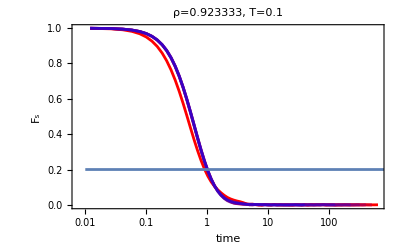
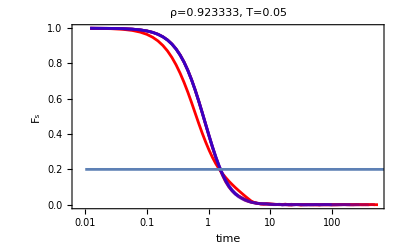
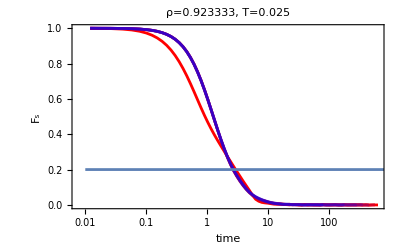
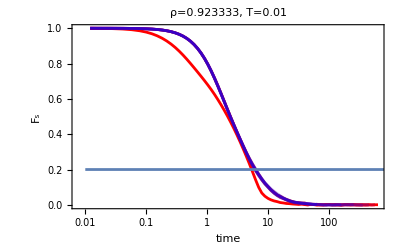
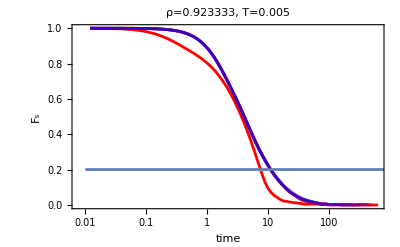
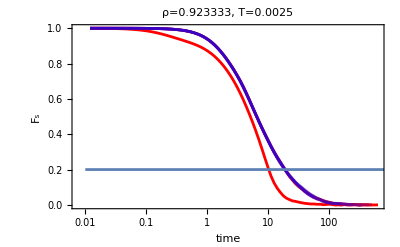
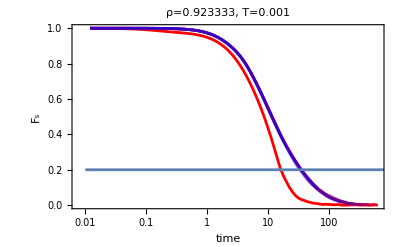
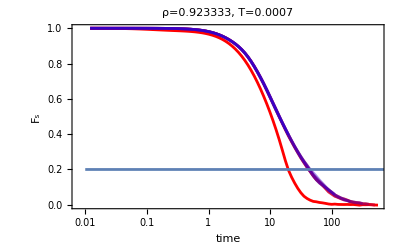

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"ρ="<>ToString[rhos[[rho]]]<>", T="<>ToString[AccountingForm[temperatures[[rho,T]]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}]
```

```mathematica
tauAlpha={{1,1.5,2.5,6,11,19,35,45,71,90}};
```

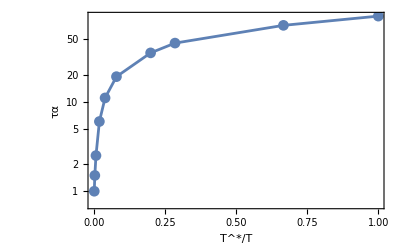

```mathematica
tauAlphaEp100kTPlot=Table[ListLogPlot[Table[{temperatures[[rho,Length[tauAlpha[[rho]]]]]/temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T^*/T","τα"},Joined->True],{rho,1}]
```

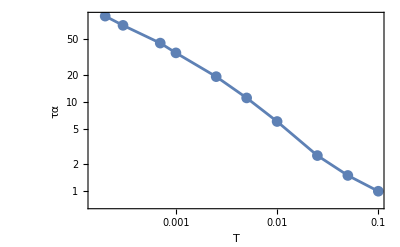

```mathematica
tauAlphaEp100kTPlotLogLog=Table[ListLogLogPlot[Table[{temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T","τα"},Joined->True],{rho,1}]
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kT.jpeg",tauAlphaEp100kTPlot[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kTLogLog.jpeg",tauAlphaEp100kTPlotLogLog[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT.jpeg",Grid[Partition[fsksPlot[[1,;;9]],3]],ImageResolution->300];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT_All.jpeg",Grid[Partition[fsksPlot[[1]],5]],ImageResolution->300];
```

### ϵ_bond=100.0kT for revcross, ϵ_spring=1.0kT for revcross

```mathematica
rhos={0.923333};
temperatures={{0.1,0.05,0.025,0.01,0.005,0.0025,0.001,0.0007,0.0003,0.0002}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/springkTRevEp100kT/rho0.923333/dynamics/Fs_T0.00100000_rho0.923333_wait100000_k7.0.csv","CSV"];
```

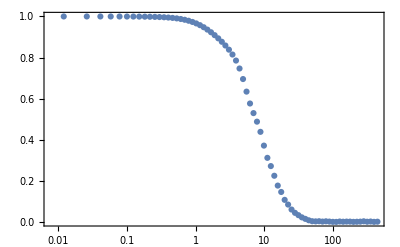

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

```mathematica
fsks=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/springkTRevEp100kT/rho","/dynamics/Fs_T","_rho","_wait","_k8.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],100000*(wt-1)},{6,8,6,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/springkTRevEp100kT/rho0.923333/dynamics/Fs_T0.10000000_rho0.923333_wait700000_k8.0.csv not found during Import.

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/springkTRevEp100kT/rho0.923333/dynamics/Fs_T0.10000000_rho0.923333_wait800000_k8.0.csv not found during Import.

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/springkTRevEp100kT/rho0.923333/dynamics/Fs_T0.10000000_rho0.923333_wait900000_k8.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
fsks[[1,2,3]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999771307902312612},{0.0260000000000000023,0.998927903012059804},{0.0410000000000000017,0.997341261180982541},{0.0580000000000000029,0.994703746140828127},{0.0779999999999999999,0.9904918971800174},{0.100000000000000006,0.984533957042731722},{0.123999999999999999,0.976545394256684518},{0.150999999999999995,0.965841636711015306},{0.181999999999999995,0.951520876475550836},{0.215999999999999998,0.933608209468088979},{0.255000000000000004,0.91063777198470941},{0.297999999999999987,0.882846380994267155},{0.347000000000000031,0.848717100125015445},{0.401000000000000023,0.808974891277051134},{0.462000000000000022,0.762593356061524674},{0.531000000000000028,0.709524214988034307},{0.607999999999999985,0.651153630910284997},{0.694000000000000061,0.588534881311457814},{0.791000000000000036,0.522660708122160367},{0.900000000000000022,0.455888949812410682},{1.02200000000000002,0.390465917138967278},{1.15900000000000003,0.327732678865483629},{1.31299999999999995,0.269804930866816228},{1.4850000000000001,0.218284771734488015},{1.67799999999999994,0.17362033047992026},{1.89500000000000002,0.135974803333589522},{2.13900000000000023,0.105754349104526607},{2.41199999999999992,0.08176216523987892},{2.71799999999999997,0.0627951507673986803},{3.06200000000000028,0.0481325560473253242},{3.44799999999999995,0.0353488360631961374},{3.88100000000000023,0.0250829215639332276},{4.36699999999999999,0.0186043288896313233},{4.91199999999999992,0.0139241779571928903},{5.52299999999999969,0.0101535829817273396},{6.20999999999999996,0.00718672747203630367},{6.97900000000000009,0.00581252778932878772},{7.84299999999999997,0.00344258281572386998},{8.81300000000000061,0.00336495572380923627},{9.90000000000000036,0.00167950785019164517},{11.120000000000001,0.000995990842492189277},{12.4890000000000008,0.00120176126782240507},{14.0250000000000004,0.0015050921853592956},{15.7490000000000006,-0.000927656354819644488},{17.6829999999999998,-0.000687422070012133494},{19.8530000000000015,-0.00192508623711494737},{22.286999999999999,-0.00281895863220567701},{25.0190000000000019,0.000683556527937620906},{28.0839999999999996,0.00129214594302444756},{31.5229999999999997,0.0000119288265033148779},{35.3810000000000002,0.00035319455142224709},{39.7109999999999985,0.00103923358083181459},{44.5679999999999978,-0.00141616348877644143},{50.0189999999999984,-0.000146764128834238518},{56.1340000000000003,0.00165446518148847674},{62.9960000000000022,-0.00169234864447169453},{70.6950000000000074,0.00123408944653081477},{79.3329999999999984,0.000151734165332222462},{89.0250000000000057,-0.00034340665602991435},{99.9000000000000057,-0.00148153850284606765},{112.102000000000004,-0.000944309001112374137},{125.793000000000006,-0.000696473862697735702},{141.153999999999996,-0.000352968690512930742},{158.38900000000001,0.0000868005361750269125},{177.728000000000009,0.000325931661294894719}}

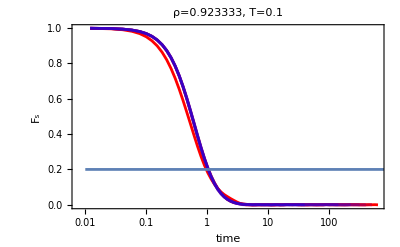
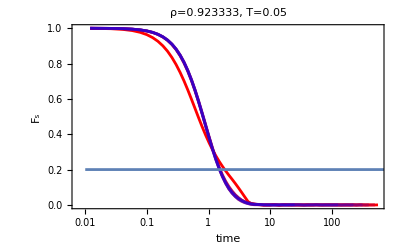
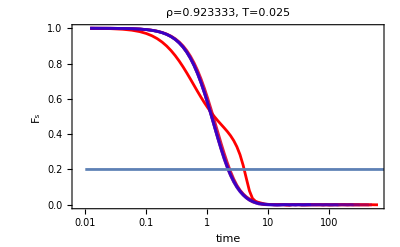
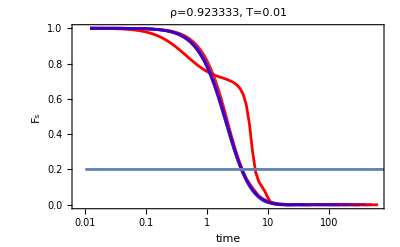
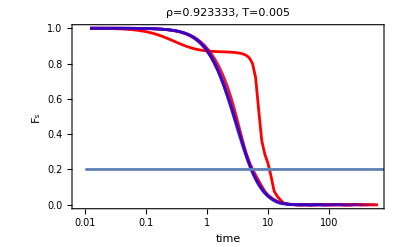
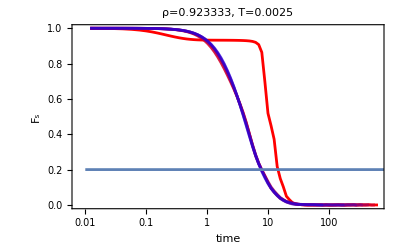
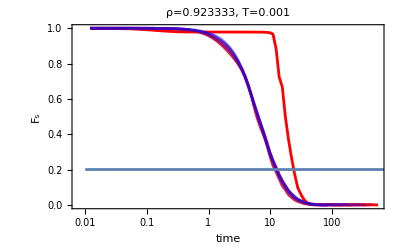
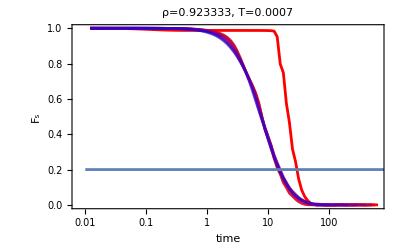

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"ρ="<>ToString[rhos[[rho]]]<>", T="<>ToString[AccountingForm[temperatures[[rho,T]]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}]
```

```mathematica
tauAlpha={{1,1.5,2.5,6,11,19,35,45,71,90}};
```

```mathematica
tauAlphaEp100kTPlot=Table[ListLogPlot[Table[{temperatures[[rho,Length[tauAlpha[[rho]]]]]/temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T^*/T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
tauAlphaEp100kTPlotLogLog=Table[ListLogLogPlot[Table[{temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kT.jpeg",tauAlphaEp100kTPlot[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kTLogLog.jpeg",tauAlphaEp100kTPlotLogLog[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT.jpeg",Grid[Partition[fsksPlot[[1,;;9]],3]],ImageResolution->300];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT_All.jpeg",Grid[Partition[fsksPlot[[1]],5]],ImageResolution->300];
```

### ϵ_bond=100,1000,10000 revcross, ϵ_spring=1.0 for revcross

```mathematica
rhos={0.923333};
temperatures={{0.1,0.01,0.001,0.0001}};
eps={100,1000,10000};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/RevEp/rho0.923333/dynamics/Fs_T0.00100000_rho0.923333_ep1000_wait0_k8.0.csv","CSV"];
```

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

-Graphics-

```mathematica
fsks=

Table[Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/RevEp/rho","/dynamics/Fs_T","_rho","_ep","_wait","_k8.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],eps[[ep]],100000*(wt-1)},{6,8,6,0,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}],{ep,Length[eps]}];
```

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/RevEp/rho0.923333/dynamics/Fs_T0.10000000_rho0.923333_ep100_wait400000_k8.0.csv not found during Import.

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/RevEp/rho0.923333/dynamics/Fs_T0.10000000_rho0.923333_ep100_wait500000_k8.0.csv not found during Import.

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/RevEp/rho0.923333/dynamics/Fs_T0.10000000_rho0.923333_ep100_wait600000_k8.0.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
fsks[[1,2,3]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999771307902312612},{0.0260000000000000023,0.998927903012059804},{0.0410000000000000017,0.997341261180982541},{0.0580000000000000029,0.994703746140828127},{0.0779999999999999999,0.9904918971800174},{0.100000000000000006,0.984533957042731722},{0.123999999999999999,0.976545394256684518},{0.150999999999999995,0.965841636711015306},{0.181999999999999995,0.951520876475550836},{0.215999999999999998,0.933608209468088979},{0.255000000000000004,0.91063777198470941},{0.297999999999999987,0.882846380994267155},{0.347000000000000031,0.848717100125015445},{0.401000000000000023,0.808974891277051134},{0.462000000000000022,0.762593356061524674},{0.531000000000000028,0.709524214988034307},{0.607999999999999985,0.651153630910284997},{0.694000000000000061,0.588534881311457814},{0.791000000000000036,0.522660708122160367},{0.900000000000000022,0.455888949812410682},{1.02200000000000002,0.390465917138967278},{1.15900000000000003,0.327732678865483629},{1.31299999999999995,0.269804930866816228},{1.4850000000000001,0.218284771734488015},{1.67799999999999994,0.17362033047992026},{1.89500000000000002,0.135974803333589522},{2.13900000000000023,0.105754349104526607},{2.41199999999999992,0.08176216523987892},{2.71799999999999997,0.0627951507673986803},{3.06200000000000028,0.0481325560473253242},{3.44799999999999995,0.0353488360631961374},{3.88100000000000023,0.0250829215639332276},{4.36699999999999999,0.0186043288896313233},{4.91199999999999992,0.0139241779571928903},{5.52299999999999969,0.0101535829817273396},{6.20999999999999996,0.00718672747203630367},{6.97900000000000009,0.00581252778932878772},{7.84299999999999997,0.00344258281572386998},{8.81300000000000061,0.00336495572380923627},{9.90000000000000036,0.00167950785019164517},{11.120000000000001,0.000995990842492189277},{12.4890000000000008,0.00120176126782240507},{14.0250000000000004,0.0015050921853592956},{15.7490000000000006,-0.000927656354819644488},{17.6829999999999998,-0.000687422070012133494},{19.8530000000000015,-0.00192508623711494737},{22.286999999999999,-0.00281895863220567701},{25.0190000000000019,0.000683556527937620906},{28.0839999999999996,0.00129214594302444756},{31.5229999999999997,0.0000119288265033148779},{35.3810000000000002,0.00035319455142224709},{39.7109999999999985,0.00103923358083181459},{44.5679999999999978,-0.00141616348877644143},{50.0189999999999984,-0.000146764128834238518},{56.1340000000000003,0.00165446518148847674},{62.9960000000000022,-0.00169234864447169453},{70.6950000000000074,0.00123408944653081477},{79.3329999999999984,0.000151734165332222462},{89.0250000000000057,-0.00034340665602991435},{99.9000000000000057,-0.00148153850284606765},{112.102000000000004,-0.000944309001112374137},{125.793000000000006,-0.000696473862697735702},{141.153999999999996,-0.000352968690512930742},{158.38900000000001,0.0000868005361750269125},{177.728000000000009,0.000325931661294894719}}

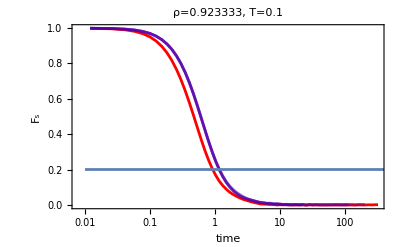
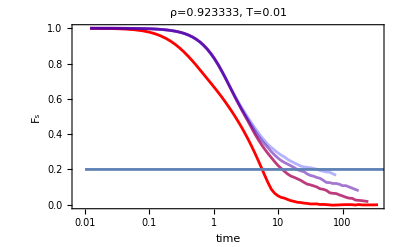
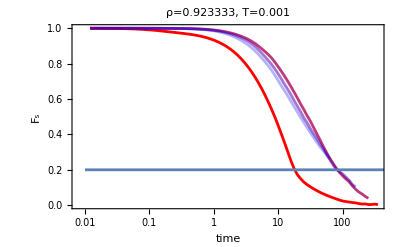
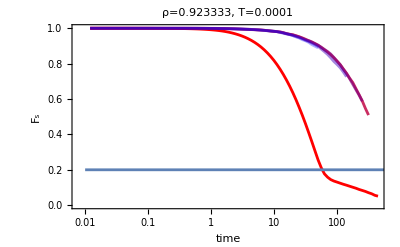
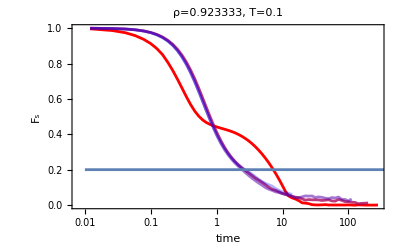
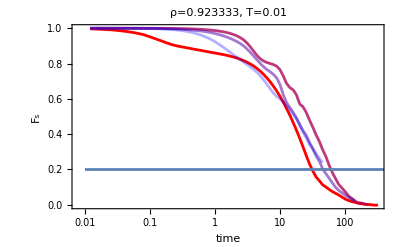
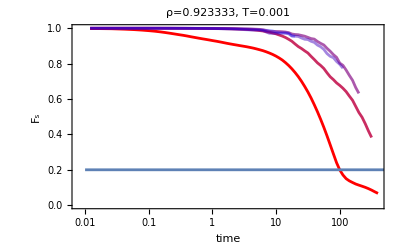
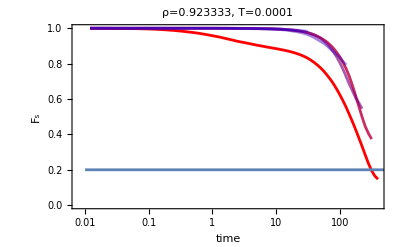

```mathematica
fsksPlot=Table[Table[Table[Show[ListLogLinearPlot[fsks[[ep,rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[ep,rho,T]]]],Joined->True,PlotLabel->"ρ="<>ToString[rhos[[rho]]]<>", T="<>ToString[AccountingForm[temperatures[[rho,T]]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}],{ep,Length[eps]}]
```

```mathematica
tauAlpha={{1,1.5,2.5,6,11,19,35,45,71,90}};
```

```mathematica
tauAlphaEp100kTPlot=Table[ListLogPlot[Table[{temperatures[[rho,Length[tauAlpha[[rho]]]]]/temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T^*/T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
tauAlphaEp100kTPlotLogLog=Table[ListLogLogPlot[Table[{temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kT.jpeg",tauAlphaEp100kTPlot[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kTLogLog.jpeg",tauAlphaEp100kTPlotLogLog[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT.jpeg",Grid[Partition[fsksPlot[[1,;;9]],3]],ImageResolution->300];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT_All.jpeg",Grid[Partition[fsksPlot[[1]],5]],ImageResolution->300];
```

### ϵ_bond=100kt revcross, FENE

```mathematica
rhos={0.923333};
temperatures={{0.1,0.01,0.001,0.0001}};
eps={100};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/RevEp100KTFENE","CSV"];
```

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

-Graphics-

```mathematica
fsks=

Table[Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/RevEp100KTFENE/rho","/dynamics/Fs_T","_rho","_ep","_wait","_k8.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],eps[[ep]]*temperatures[[rho,T]],100000*(wt-1)},{6,8,6,6,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}],{ep,Length[eps]}];
```

```mathematica
fsks[[1,2,3]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999771307902312612},{0.0260000000000000023,0.998927903012059804},{0.0410000000000000017,0.997341261180982541},{0.0580000000000000029,0.994703746140828127},{0.0779999999999999999,0.9904918971800174},{0.100000000000000006,0.984533957042731722},{0.123999999999999999,0.976545394256684518},{0.150999999999999995,0.965841636711015306},{0.181999999999999995,0.951520876475550836},{0.215999999999999998,0.933608209468088979},{0.255000000000000004,0.91063777198470941},{0.297999999999999987,0.882846380994267155},{0.347000000000000031,0.848717100125015445},{0.401000000000000023,0.808974891277051134},{0.462000000000000022,0.762593356061524674},{0.531000000000000028,0.709524214988034307},{0.607999999999999985,0.651153630910284997},{0.694000000000000061,0.588534881311457814},{0.791000000000000036,0.522660708122160367},{0.900000000000000022,0.455888949812410682},{1.02200000000000002,0.390465917138967278},{1.15900000000000003,0.327732678865483629},{1.31299999999999995,0.269804930866816228},{1.4850000000000001,0.218284771734488015},{1.67799999999999994,0.17362033047992026},{1.89500000000000002,0.135974803333589522},{2.13900000000000023,0.105754349104526607},{2.41199999999999992,0.08176216523987892},{2.71799999999999997,0.0627951507673986803},{3.06200000000000028,0.0481325560473253242},{3.44799999999999995,0.0353488360631961374},{3.88100000000000023,0.0250829215639332276},{4.36699999999999999,0.0186043288896313233},{4.91199999999999992,0.0139241779571928903},{5.52299999999999969,0.0101535829817273396},{6.20999999999999996,0.00718672747203630367},{6.97900000000000009,0.00581252778932878772},{7.84299999999999997,0.00344258281572386998},{8.81300000000000061,0.00336495572380923627},{9.90000000000000036,0.00167950785019164517},{11.120000000000001,0.000995990842492189277},{12.4890000000000008,0.00120176126782240507},{14.0250000000000004,0.0015050921853592956},{15.7490000000000006,-0.000927656354819644488},{17.6829999999999998,-0.000687422070012133494},{19.8530000000000015,-0.00192508623711494737},{22.286999999999999,-0.00281895863220567701},{25.0190000000000019,0.000683556527937620906},{28.0839999999999996,0.00129214594302444756},{31.5229999999999997,0.0000119288265033148779},{35.3810000000000002,0.00035319455142224709},{39.7109999999999985,0.00103923358083181459},{44.5679999999999978,-0.00141616348877644143},{50.0189999999999984,-0.000146764128834238518},{56.1340000000000003,0.00165446518148847674},{62.9960000000000022,-0.00169234864447169453},{70.6950000000000074,0.00123408944653081477},{79.3329999999999984,0.000151734165332222462},{89.0250000000000057,-0.00034340665602991435},{99.9000000000000057,-0.00148153850284606765},{112.102000000000004,-0.000944309001112374137},{125.793000000000006,-0.000696473862697735702},{141.153999999999996,-0.000352968690512930742},{158.38900000000001,0.0000868005361750269125},{177.728000000000009,0.000325931661294894719}}

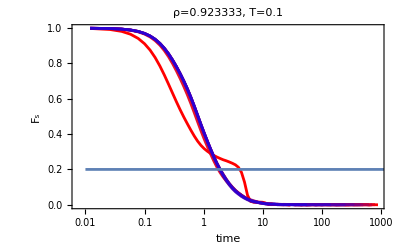
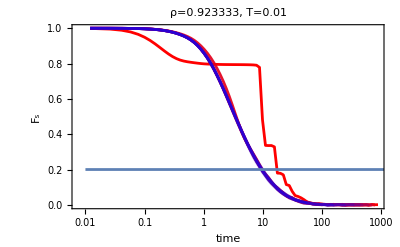
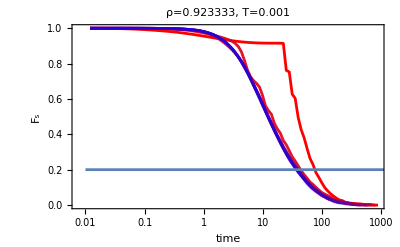
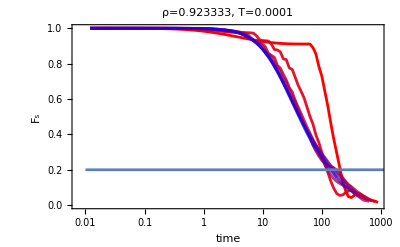

```mathematica
fsksPlot=Table[Table[Table[Show[ListLogLinearPlot[fsks[[ep,rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[ep,rho,T]]]],Joined->True,PlotLabel->"ρ="<>ToString[rhos[[rho]]]<>", T="<>ToString[AccountingForm[temperatures[[rho,T]]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}],{ep,Length[eps]}]
```

```mathematica
tauAlpha={{2,9,35,150}};
```

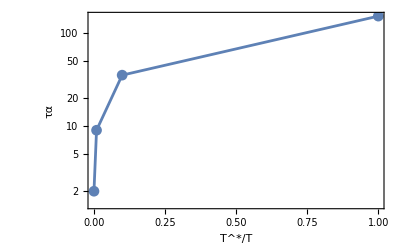

```mathematica
tauAlphaEp100kTPlot=Table[ListLogPlot[Table[{temperatures[[rho,Length[tauAlpha[[rho]]]]]/temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T^*/T","τα"},Joined->True],{rho,1}]
```

```mathematica
tauAlphaEp100kTPlotLogLog=Table[ListLogLogPlot[Table[{temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kT.jpeg",tauAlphaEp100kTPlot[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kTLogLog.jpeg",tauAlphaEp100kTPlotLogLog[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT.jpeg",Grid[Partition[fsksPlot[[1,;;9]],3]],ImageResolution->300];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT_All.jpeg",Grid[Partition[fsksPlot[[1]],5]],ImageResolution->300];
```

### ϵ_bond=100kt revcross, spring with WCA corrected

```mathematica
rhos={0.923333};
temperatures={{0.1,0.01,0.001,0.0001}};
eps={100};
```

```mathematica
test1=Import["/home/chengling/Research/Project/vitrimer/data/test/RevEp/rho0.923333/static/gr_avg_T0.00100000_rho0.923333_ep100.csv","CSV"];
```

```mathematica
test4=Import["/home/chengling/Research/Project/vitrimer/data/test/RevEp/rho0.923333/static/gr_avg_T0.00100000_rho0.923333_ep1000.csv","CSV"];
```

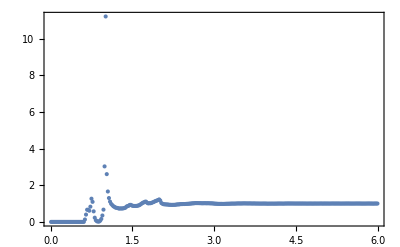

```mathematica
ListPlot[test4[[2;;]],PlotRange->All]
```

```mathematica
test2=Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/g/g_T0.001_rho0.92333.dat","Data"];
```

```mathematica
test3=Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/g/g_T0.001_rho1.80845.dat","Data"];
```

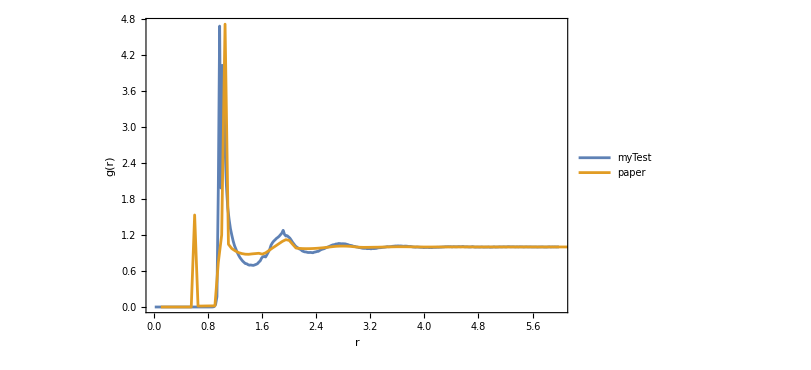

```mathematica
grPlot=ListPlot[{test1[[2;;]],test2[[;;,1;;2]]},PlotRange->{{0,6},All},Joined->True,PlotMarkers->None,ImageSize->600,FrameLabel->{"r","g(r)"},PlotLegends->{"myTest","paper"}]
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_18/grPlot.jpeg",grPlot,ImageResolution->300];
```

```mathematica
Floor[eps[[1]]*temperatures[[1,4]]]
```

0

```mathematica
fsks=

Table[Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/RevEp/rho","/dynamics/Fs_T","_rho","_ep","_wait","_k20.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],Floor[eps[[ep]]*temperatures[[rho,T]]],100000*(wt-1)},{6,8,6,0,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}],{ep,Length[eps]}];
```

```mathematica
fsks[[1,2,3]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999771307902312612},{0.0260000000000000023,0.998927903012059804},{0.0410000000000000017,0.997341261180982541},{0.0580000000000000029,0.994703746140828127},{0.0779999999999999999,0.9904918971800174},{0.100000000000000006,0.984533957042731722},{0.123999999999999999,0.976545394256684518},{0.150999999999999995,0.965841636711015306},{0.181999999999999995,0.951520876475550836},{0.215999999999999998,0.933608209468088979},{0.255000000000000004,0.91063777198470941},{0.297999999999999987,0.882846380994267155},{0.347000000000000031,0.848717100125015445},{0.401000000000000023,0.808974891277051134},{0.462000000000000022,0.762593356061524674},{0.531000000000000028,0.709524214988034307},{0.607999999999999985,0.651153630910284997},{0.694000000000000061,0.588534881311457814},{0.791000000000000036,0.522660708122160367},{0.900000000000000022,0.455888949812410682},{1.02200000000000002,0.390465917138967278},{1.15900000000000003,0.327732678865483629},{1.31299999999999995,0.269804930866816228},{1.4850000000000001,0.218284771734488015},{1.67799999999999994,0.17362033047992026},{1.89500000000000002,0.135974803333589522},{2.13900000000000023,0.105754349104526607},{2.41199999999999992,0.08176216523987892},{2.71799999999999997,0.0627951507673986803},{3.06200000000000028,0.0481325560473253242},{3.44799999999999995,0.0353488360631961374},{3.88100000000000023,0.0250829215639332276},{4.36699999999999999,0.0186043288896313233},{4.91199999999999992,0.0139241779571928903},{5.52299999999999969,0.0101535829817273396},{6.20999999999999996,0.00718672747203630367},{6.97900000000000009,0.00581252778932878772},{7.84299999999999997,0.00344258281572386998},{8.81300000000000061,0.00336495572380923627},{9.90000000000000036,0.00167950785019164517},{11.120000000000001,0.000995990842492189277},{12.4890000000000008,0.00120176126782240507},{14.0250000000000004,0.0015050921853592956},{15.7490000000000006,-0.000927656354819644488},{17.6829999999999998,-0.000687422070012133494},{19.8530000000000015,-0.00192508623711494737},{22.286999999999999,-0.00281895863220567701},{25.0190000000000019,0.000683556527937620906},{28.0839999999999996,0.00129214594302444756},{31.5229999999999997,0.0000119288265033148779},{35.3810000000000002,0.00035319455142224709},{39.7109999999999985,0.00103923358083181459},{44.5679999999999978,-0.00141616348877644143},{50.0189999999999984,-0.000146764128834238518},{56.1340000000000003,0.00165446518148847674},{62.9960000000000022,-0.00169234864447169453},{70.6950000000000074,0.00123408944653081477},{79.3329999999999984,0.000151734165332222462},{89.0250000000000057,-0.00034340665602991435},{99.9000000000000057,-0.00148153850284606765},{112.102000000000004,-0.000944309001112374137},{125.793000000000006,-0.000696473862697735702},{141.153999999999996,-0.000352968690512930742},{158.38900000000001,0.0000868005361750269125},{177.728000000000009,0.000325931661294894719}}

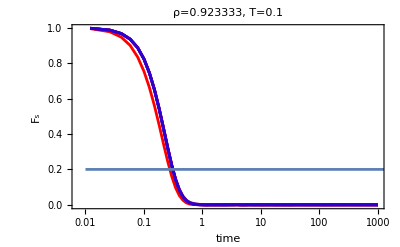
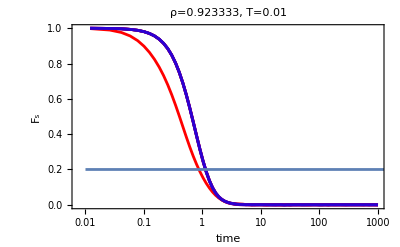
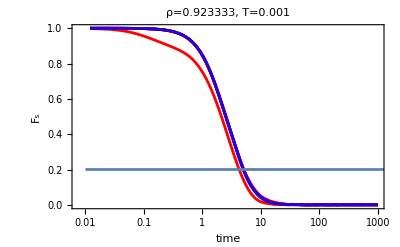
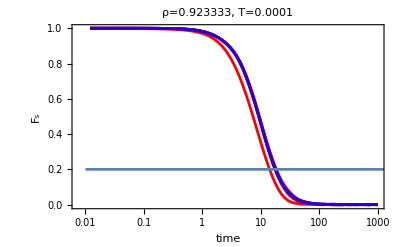

```mathematica
fsksPlot=Table[Table[Table[Show[ListLogLinearPlot[fsks[[ep,rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[ep,rho,T]]]],Joined->True,PlotLabel->"ρ="<>ToString[rhos[[rho]]]<>", T="<>ToString[AccountingForm[temperatures[[rho,T]]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}],{ep,Length[eps]}]
```

```mathematica
tauAlpha={{1,6,35,130}};
```

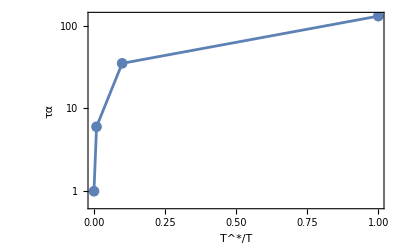

```mathematica
tauAlphaEp100kTPlot=Table[ListLogPlot[Table[{temperatures[[rho,Length[tauAlpha[[rho]]]]]/temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T^*/T","τα"},Joined->True],{rho,1}]
```

```mathematica
tauAlphaEp100kTPlotLogLog=Table[ListLogLogPlot[Table[{temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kT.jpeg",tauAlphaEp100kTPlot[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kTLogLog.jpeg",tauAlphaEp100kTPlotLogLog[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT.jpeg",Grid[Partition[fsksPlot[[1,;;9]],3]],ImageResolution->300];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT_All.jpeg",Grid[Partition[fsksPlot[[1]],5]],ImageResolution->300];
```

### ϵ_bond=10,50kT revcross, ϵ_spring=1.0 for revcross

```mathematica
rhos={0.923333};
temperatures={{0.1,0.01,0.001,0.0001}};
eps={10,50};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/RevEp/rho0.923333/dynamics/Fs_T0.00100000_rho0.923333_ep0.01000000_wait1000000_k9","CSV"];
```

Import::nffil: File /home/chengling/Research/Project/vitrimer/data/test/RevEp/rho0.923333/dynamics/Fs_T0.00100000_rho0.923333_ep0.01000000_wait1000000_k7.4 not found during Import.

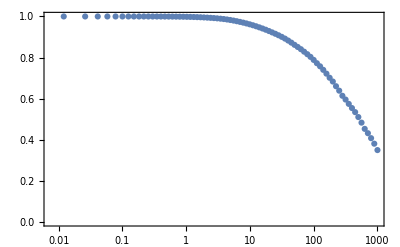

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

```mathematica
fsks=

Table[Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/RevEp/rho","/dynamics/Fs_T","_rho","_ep","_wait","_k9.2.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],eps[[ep]]*temperatures[[rho,T]],100000*(wt-1)},{6,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}],{ep,Length[eps]}];
```

```mathematica
fsks[[1,2,3]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999771307902312612},{0.0260000000000000023,0.998927903012059804},{0.0410000000000000017,0.997341261180982541},{0.0580000000000000029,0.994703746140828127},{0.0779999999999999999,0.9904918971800174},{0.100000000000000006,0.984533957042731722},{0.123999999999999999,0.976545394256684518},{0.150999999999999995,0.965841636711015306},{0.181999999999999995,0.951520876475550836},{0.215999999999999998,0.933608209468088979},{0.255000000000000004,0.91063777198470941},{0.297999999999999987,0.882846380994267155},{0.347000000000000031,0.848717100125015445},{0.401000000000000023,0.808974891277051134},{0.462000000000000022,0.762593356061524674},{0.531000000000000028,0.709524214988034307},{0.607999999999999985,0.651153630910284997},{0.694000000000000061,0.588534881311457814},{0.791000000000000036,0.522660708122160367},{0.900000000000000022,0.455888949812410682},{1.02200000000000002,0.390465917138967278},{1.15900000000000003,0.327732678865483629},{1.31299999999999995,0.269804930866816228},{1.4850000000000001,0.218284771734488015},{1.67799999999999994,0.17362033047992026},{1.89500000000000002,0.135974803333589522},{2.13900000000000023,0.105754349104526607},{2.41199999999999992,0.08176216523987892},{2.71799999999999997,0.0627951507673986803},{3.06200000000000028,0.0481325560473253242},{3.44799999999999995,0.0353488360631961374},{3.88100000000000023,0.0250829215639332276},{4.36699999999999999,0.0186043288896313233},{4.91199999999999992,0.0139241779571928903},{5.52299999999999969,0.0101535829817273396},{6.20999999999999996,0.00718672747203630367},{6.97900000000000009,0.00581252778932878772},{7.84299999999999997,0.00344258281572386998},{8.81300000000000061,0.00336495572380923627},{9.90000000000000036,0.00167950785019164517},{11.120000000000001,0.000995990842492189277},{12.4890000000000008,0.00120176126782240507},{14.0250000000000004,0.0015050921853592956},{15.7490000000000006,-0.000927656354819644488},{17.6829999999999998,-0.000687422070012133494},{19.8530000000000015,-0.00192508623711494737},{22.286999999999999,-0.00281895863220567701},{25.0190000000000019,0.000683556527937620906},{28.0839999999999996,0.00129214594302444756},{31.5229999999999997,0.0000119288265033148779},{35.3810000000000002,0.00035319455142224709},{39.7109999999999985,0.00103923358083181459},{44.5679999999999978,-0.00141616348877644143},{50.0189999999999984,-0.000146764128834238518},{56.1340000000000003,0.00165446518148847674},{62.9960000000000022,-0.00169234864447169453},{70.6950000000000074,0.00123408944653081477},{79.3329999999999984,0.000151734165332222462},{89.0250000000000057,-0.00034340665602991435},{99.9000000000000057,-0.00148153850284606765},{112.102000000000004,-0.000944309001112374137},{125.793000000000006,-0.000696473862697735702},{141.153999999999996,-0.000352968690512930742},{158.38900000000001,0.0000868005361750269125},{177.728000000000009,0.000325931661294894719}}

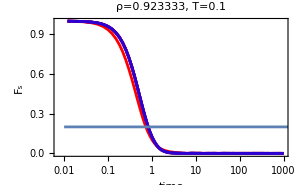
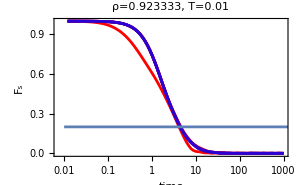
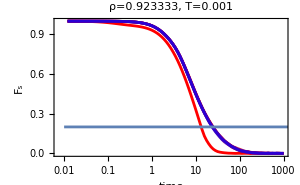
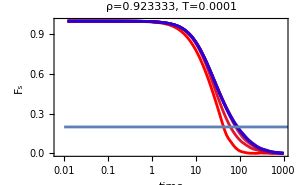
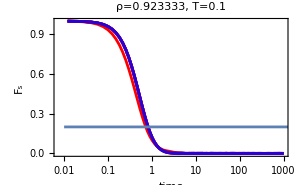
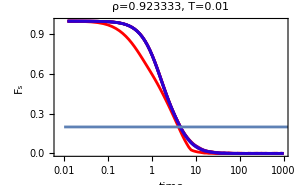
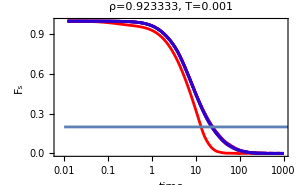
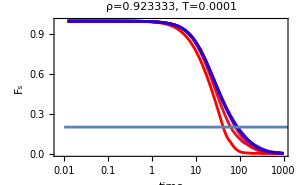

```mathematica
fsksPlot=Table[Table[Table[Show[ListLogLinearPlot[fsks[[ep,rho,T,;;,2;;]],ImageSize->300,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[ep,rho,T]]]],Joined->True,PlotLabel->"ρ="<>ToString[rhos[[rho]]]<>", T="<>ToString[AccountingForm[temperatures[[rho,T]]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}],{ep,Length[eps]}]
```

```mathematica
tauAlpha={{1,1.5,2.5,6,11,19,35,45,71,90}};
```

```mathematica
tauAlphaEp100kTPlot=Table[ListLogPlot[Table[{temperatures[[rho,Length[tauAlpha[[rho]]]]]/temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T^*/T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
tauAlphaEp100kTPlotLogLog=Table[ListLogLogPlot[Table[{temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kT.jpeg",tauAlphaEp100kTPlot[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kTLogLog.jpeg",tauAlphaEp100kTPlotLogLog[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT.jpeg",Grid[Partition[fsksPlot[[1,;;9]],3]],ImageResolution->300];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT_All.jpeg",Grid[Partition[fsksPlot[[1]],5]],ImageResolution->300];
```

### paper parameters

```mathematica
rhos={0.923333};
temperatures={{0.1,0.01,0.001,0.0001}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVE_softStart/rho0.923333/dynamics/Fs_T0.00010000_rho0.923333_wait500000_k6.0.csv","CSV"];
```

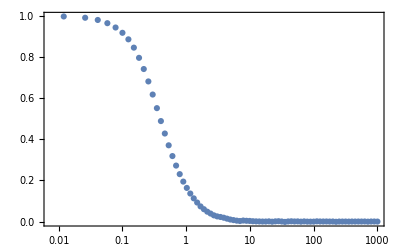

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

```mathematica
fsks=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVE_softStart/rho","/dynamics/Fs_T","_rho","_wait","_k6.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],100000*(wt-1)},{6,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]]
```

{{1.×10^-6,1},{0.001,0.999998},{0.002,0.999993},{0.003,0.999983},{0.004,0.999971},{0.005,0.999954},{0.006,0.999935},{0.007,0.999911},{0.008,0.999885},{0.009,0.999855},{0.01,0.999822},{0.02,0.999308},{0.03,0.998488},{0.04,0.997409},{0.05,0.996127},{0.06,0.994675},{0.07,0.993088},{0.08,0.991369},{0.09,0.989514},{0.1,0.987507},{0.2,0.95703},{0.3,0.911648},{0.4,0.856424},{0.5,0.79606},{0.6,0.733635},{0.7,0.67194},{0.8,0.612818},{0.9,0.557291},{1,0.505994},{2,0.201778},{3,0.0960446},{4,0.0535727},{5,0.0327748},{6,0.020956},{7,0.0144412},{8,0.0108028},{9,0.00782143}}

```mathematica
fskspaper={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-06_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

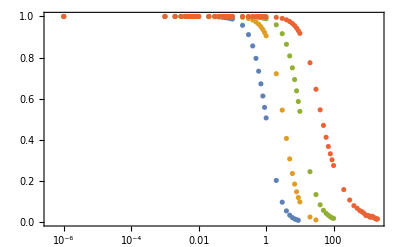

```mathematica
ListLogLinearPlot[fskspaper]
```

```mathematica
fskspaper
```

```mathematica
fsks[[1,2,3]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999975390285547494},{0.0260000000000000023,0.999904803627002181},{0.0410000000000000017,0.99978540642255298},{0.0580000000000000029,0.999633468899338573},{0.0779999999999999999,0.9994139596848024},{0.100000000000000006,0.999110850399954731},{0.123999999999999999,0.998738859011941038},{0.150999999999999995,0.998186028819485482},{0.181999999999999995,0.997434452992618237},{0.215999999999999998,0.996446743341604879},{0.255000000000000004,0.995144829108778217},{0.297999999999999987,0.993470445708836025},{0.347000000000000031,0.991241639712710954},{0.401000000000000023,0.988418668522562993},{0.462000000000000022,0.984759658351755163},{0.531000000000000028,0.979958605338805411},{0.607999999999999985,0.973965899439223515},{0.694000000000000061,0.966503218942779685},{0.791000000000000036,0.95711699165169184},{0.900000000000000022,0.945621476270694372},{1.02200000000000002,0.931515862270163919},{1.15900000000000003,0.914625473506135545},{1.31299999999999995,0.894970452718984788},{1.4850000000000001,0.873158084421812308},{1.67799999999999994,0.850018970026783172},{1.89500000000000002,0.826388382574565372},{2.13900000000000023,0.803326675062767559},{2.41199999999999992,0.782257371731480466},{2.71799999999999997,0.763899722657140901},{3.06200000000000028,0.748207855990111304},{3.44799999999999995,0.734915847092047159},{3.88100000000000023,0.723483568642379615},{4.36699999999999999,0.713272222169036518},{4.91199999999999992,0.702926916008538849},{5.52299999999999969,0.690019245069017573},{6.20999999999999996,0.669124662979352136},{6.97900000000000009,0.629150990612832861},{7.84299999999999997,0.55846285549369612},{8.81300000000000061,0.490654892739116388},{9.90000000000000036,0.457570231678513073},{11.120000000000001,0.442656547931669864},{12.4890000000000008,0.430594417374045912},{14.0250000000000004,0.408737068024553285},{15.7490000000000006,0.362428005249798957},{17.6829999999999998,0.331079864768471233},{19.8530000000000015,0.32547044226773264},{22.286999999999999,0.311538231495144369},{25.0190000000000019,0.268199414585791218},{28.0839999999999996,0.262414435093795806},{31.5229999999999997,0.206478292548705172},{35.3810000000000002,0.190191286857904068},{39.7109999999999985,0.14460106684431967},{44.5679999999999978,0.105112354895571233},{50.0189999999999984,0.0938996877547176451},{56.1340000000000003,0.0918787131105552046},{62.9960000000000022,0.0863501967222342348},{70.6950000000000074,0.0688206327052851979},{79.3329999999999984,0.0519761127799926032},{89.0250000000000057,0.0409053895115075034},{99.9000000000000057,0.0309706829684774469},{112.102000000000004,0.0277596544653624273},{125.793000000000006,0.0238605770812384023},{141.153999999999996,0.0259722058528048007},{158.38900000000001,0.0251578721480017926},{177.728000000000009,0.0226547743905971578},{199.426000000000016,0.0194349533725783376},{223.771999999999991,0.0119099296526295629},{251.088999999999999,0.0142159919490155006},{281.738,0.00147998721975703732},{316.127999999999986,0.00787401412092559629},{354.713000000000022,0.00828928130170158983},{398.007000000000005,0.00377718172153741934},{446.584000000000003,0.00157788567299659162},{501.086999999999989,0.00239760872978698894},{562.240999999999985,0.00151234853102777856},{630.856999999999971,-0.000638713730601771852},{707.846000000000004,0.00179576378324767041},{794.228000000000066,0.000484746634847000582},{891.151000000000067,0.00125831390663207221},{999.899999999999977,0.00108480150404643744}}

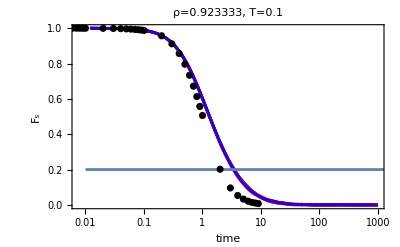
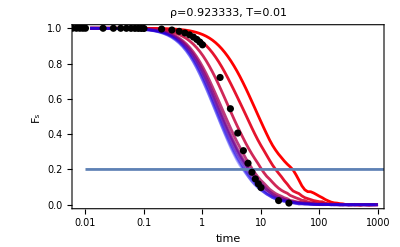
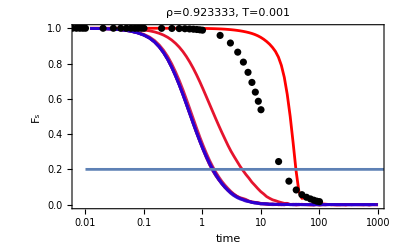
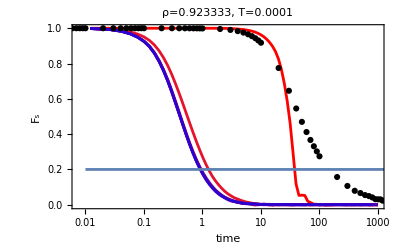

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"ρ="<>ToString[rhos[[rho]]]<>", T="<>ToString[AccountingForm[temperatures[[rho,T]]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}],ListLogLinearPlot[fskspaper[[T]],PlotStyle->{Dashed,Black}]],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}]
```

```mathematica
(*The below pictures are for nvt*)
```

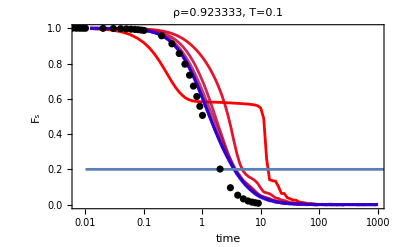
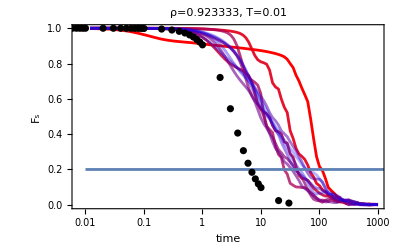
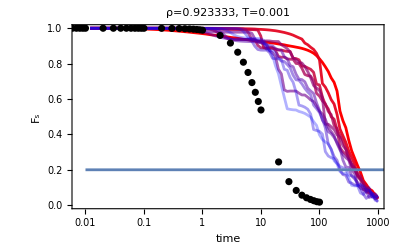
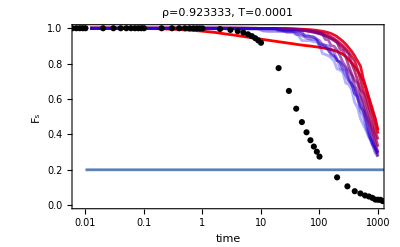
```mathematica
fsksPLot={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
tauAlpha={{1,1.5,2.5,6,11,19,35,45,71,90}};
```

```mathematica
tauAlphaEp100kTPlot=Table[ListLogPlot[Table[{temperatures[[rho,Length[tauAlpha[[rho]]]]]/temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T^*/T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
tauAlphaEp100kTPlotLogLog=Table[ListLogLogPlot[Table[{temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kT.jpeg",tauAlphaEp100kTPlot[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kTLogLog.jpeg",tauAlphaEp100kTPlotLogLog[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT.jpeg",Grid[Partition[fsksPlot[[1,;;9]],3]],ImageResolution->300];
```

```mathematica
fsksPLot
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["/home/chengling/Research/updates/2025_11_17/fs_vitrimer.jpeg",Grid[Partition[fsksPLot,2]],ImageResolution->300];
```

### paper parameters NVE

```mathematica
(*This is for dt =0.0001, NVT timesteps = 1000000*)
```

```mathematica
rhos={0.923333};
temperatures={{0.1,0.01,0.001,0.0001}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVE_softStart/rho0.923333/dynamics/Fs_T0.00010000_rho0.923333_wait500000_k6.0.csv","CSV"];
```

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

-Graphics-

```mathematica
fsks=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVE_softStart/rho","/dynamics/Fs_T","_rho","_wait","_k6.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],100000*(wt-1)},{6,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies=
Table[Table[DeleteCases[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVE_softStart/rho","/energy_T","_rho","_wait",".log"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]]},{6,8,6}],"Data"],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies
```

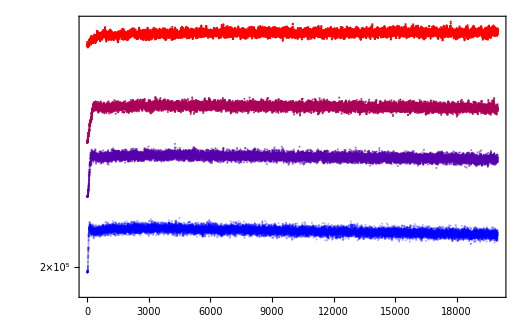

```mathematica
ListLogPlot[Abs[energies[[1,;;,2;;,1]]+energies[[1,;;,2;;,2]]],PlotStyle->redBluePlotConfig[4]]
```

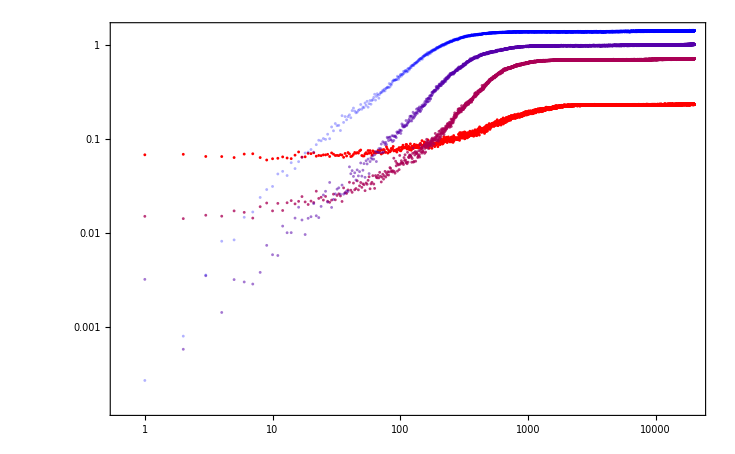

```mathematica
kineticEnergyPlot=ListLogLogPlot[energies[[1,;;,2;;,3]],PlotStyle->redBluePlotConfig[4]]
```

```mathematica
energies[[1,1,2;;,3]][[1]]
```

0.06823

```mathematica
actualT=Table[Mean[energies[[1,T,2;;,3]][[5000;;]]],{T,4}]
```

{0.233781,0.709769,1.0088,1.41663}

```mathematica
Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]]
```

{{1.×10^-6,1},{0.001,0.999998},{0.002,0.999993},{0.003,0.999983},{0.004,0.999971},{0.005,0.999954},{0.006,0.999935},{0.007,0.999911},{0.008,0.999885},{0.009,0.999855},{0.01,0.999822},{0.02,0.999308},{0.03,0.998488},{0.04,0.997409},{0.05,0.996127},{0.06,0.994675},{0.07,0.993088},{0.08,0.991369},{0.09,0.989514},{0.1,0.987507},{0.2,0.95703},{0.3,0.911648},{0.4,0.856424},{0.5,0.79606},{0.6,0.733635},{0.7,0.67194},{0.8,0.612818},{0.9,0.557291},{1,0.505994},{2,0.201778},{3,0.0960446},{4,0.0535727},{5,0.0327748},{6,0.020956},{7,0.0144412},{8,0.0108028},{9,0.00782143}}

```mathematica
fskspaper={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0022_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.007_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.015_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

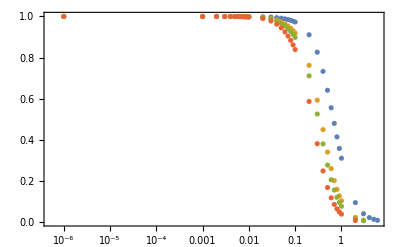

```mathematica
ListLogLinearPlot[fskspaper]
```

```mathematica
fskspaper
```

```mathematica
fsks[[1,2,3]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999975390285547494},{0.0260000000000000023,0.999904803627002181},{0.0410000000000000017,0.99978540642255298},{0.0580000000000000029,0.999633468899338573},{0.0779999999999999999,0.9994139596848024},{0.100000000000000006,0.999110850399954731},{0.123999999999999999,0.998738859011941038},{0.150999999999999995,0.998186028819485482},{0.181999999999999995,0.997434452992618237},{0.215999999999999998,0.996446743341604879},{0.255000000000000004,0.995144829108778217},{0.297999999999999987,0.993470445708836025},{0.347000000000000031,0.991241639712710954},{0.401000000000000023,0.988418668522562993},{0.462000000000000022,0.984759658351755163},{0.531000000000000028,0.979958605338805411},{0.607999999999999985,0.973965899439223515},{0.694000000000000061,0.966503218942779685},{0.791000000000000036,0.95711699165169184},{0.900000000000000022,0.945621476270694372},{1.02200000000000002,0.931515862270163919},{1.15900000000000003,0.914625473506135545},{1.31299999999999995,0.894970452718984788},{1.4850000000000001,0.873158084421812308},{1.67799999999999994,0.850018970026783172},{1.89500000000000002,0.826388382574565372},{2.13900000000000023,0.803326675062767559},{2.41199999999999992,0.782257371731480466},{2.71799999999999997,0.763899722657140901},{3.06200000000000028,0.748207855990111304},{3.44799999999999995,0.734915847092047159},{3.88100000000000023,0.723483568642379615},{4.36699999999999999,0.713272222169036518},{4.91199999999999992,0.702926916008538849},{5.52299999999999969,0.690019245069017573},{6.20999999999999996,0.669124662979352136},{6.97900000000000009,0.629150990612832861},{7.84299999999999997,0.55846285549369612},{8.81300000000000061,0.490654892739116388},{9.90000000000000036,0.457570231678513073},{11.120000000000001,0.442656547931669864},{12.4890000000000008,0.430594417374045912},{14.0250000000000004,0.408737068024553285},{15.7490000000000006,0.362428005249798957},{17.6829999999999998,0.331079864768471233},{19.8530000000000015,0.32547044226773264},{22.286999999999999,0.311538231495144369},{25.0190000000000019,0.268199414585791218},{28.0839999999999996,0.262414435093795806},{31.5229999999999997,0.206478292548705172},{35.3810000000000002,0.190191286857904068},{39.7109999999999985,0.14460106684431967},{44.5679999999999978,0.105112354895571233},{50.0189999999999984,0.0938996877547176451},{56.1340000000000003,0.0918787131105552046},{62.9960000000000022,0.0863501967222342348},{70.6950000000000074,0.0688206327052851979},{79.3329999999999984,0.0519761127799926032},{89.0250000000000057,0.0409053895115075034},{99.9000000000000057,0.0309706829684774469},{112.102000000000004,0.0277596544653624273},{125.793000000000006,0.0238605770812384023},{141.153999999999996,0.0259722058528048007},{158.38900000000001,0.0251578721480017926},{177.728000000000009,0.0226547743905971578},{199.426000000000016,0.0194349533725783376},{223.771999999999991,0.0119099296526295629},{251.088999999999999,0.0142159919490155006},{281.738,0.00147998721975703732},{316.127999999999986,0.00787401412092559629},{354.713000000000022,0.00828928130170158983},{398.007000000000005,0.00377718172153741934},{446.584000000000003,0.00157788567299659162},{501.086999999999989,0.00239760872978698894},{562.240999999999985,0.00151234853102777856},{630.856999999999971,-0.000638713730601771852},{707.846000000000004,0.00179576378324767041},{794.228000000000066,0.000484746634847000582},{891.151000000000067,0.00125831390663207221},{999.899999999999977,0.00108480150404643744}}

```mathematica
temperatures
```

{{0.1,0.01,0.001,0.0001}}

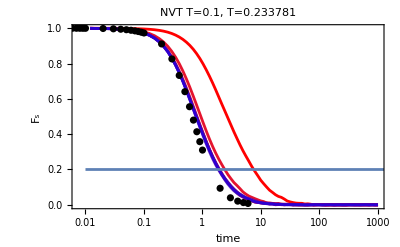
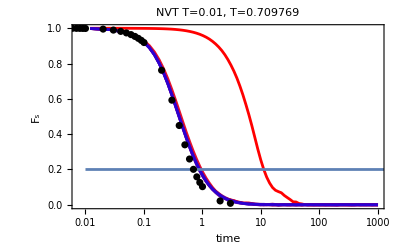
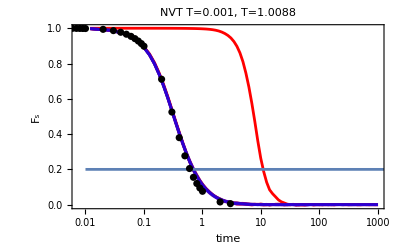
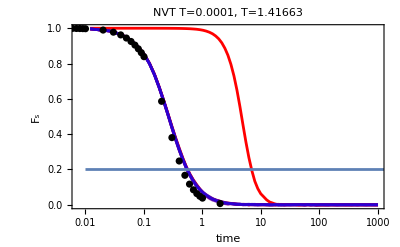

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"NVT T="<>ToString[temperatures[[rho,T]]]<>", T="<>ToString[AccountingForm[actualT[[T]]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}],ListLogLinearPlot[fskspaper[[T]],PlotStyle->{Dashed,Black}]],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}]
```

```mathematica
fsksPLot={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
tauAlpha={{1,1.5,2.5,6,11,19,35,45,71,90}};
```

```mathematica
tauAlphaEp100kTPlot=Table[ListLogPlot[Table[{temperatures[[rho,Length[tauAlpha[[rho]]]]]/temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T^*/T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
tauAlphaEp100kTPlotLogLog=Table[ListLogLogPlot[Table[{temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kT.jpeg",tauAlphaEp100kTPlot[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kTLogLog.jpeg",tauAlphaEp100kTPlotLogLog[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT.jpeg",Grid[Partition[fsksPlot[[1,;;9]],3]],ImageResolution->300];
```

```mathematica
fsksPLot
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["/home/chengling/Research/updates/2025_12_1/fs_vitrimer.jpeg",Grid[Partition[fsksPlot[[1]],2]],ImageResolution->300];
```

```mathematica
Export["/home/chengling/Research/updates/2025_12_1/kineticENergy.jpeg",kineticEnergyPlot,ImageResolution->300];
```

### paper parameters NVE longer equil

```mathematica
(*This is for dt =0.0001, NVT timesteps = 1000000*)
```

```mathematica
rhos={0.923333};
temperatures={{10.0,1.0,0.1,0.01,0.001,0.0001}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVE_softStart_longerEquil/rho0.923333/dynamics/Fs_T0.00010000_rho0.923333_NVTts10000000.0_NVTdt0.001_wait800000_k6.0.csv","CSV"];
```

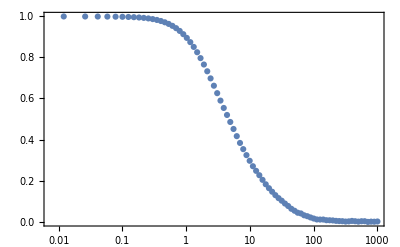

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

```mathematica
fsks=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVE_softStart_longerEquil/rho","/dynamics/Fs_T","_rho","_NVTts10000000.0_NVTdt0.001_wait","_k6.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],100000*(wt-1)},{6,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies=
Table[Table[DeleteCases[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVE_softStart_longerEquil/rho","/energy_T","_rho","_NVTts10000000.0_NVTdt0.001.log"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]]},{6,8,6}],"Data"],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies
```

```mathematica
totalEnergy=energies[[1,;;,2;;,1]]+energies[[1,;;,2;;,2]];
```

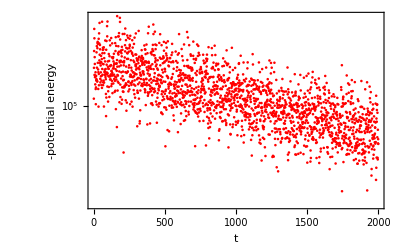
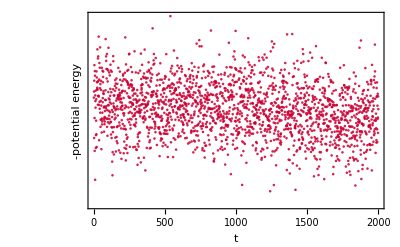
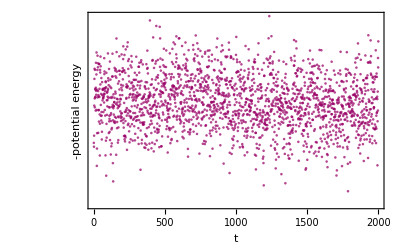
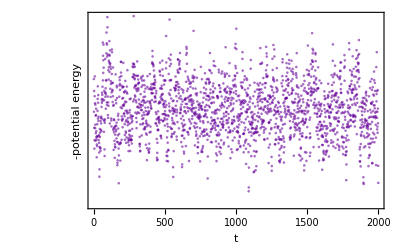
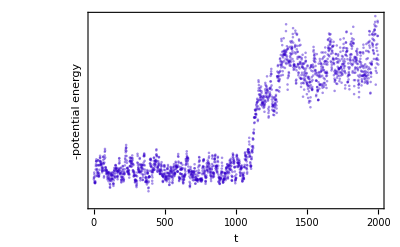
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
potentialEPlots=Table[ListLogPlot[-energies[[1,T,2;;,1]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","-potential energy"},ImageSize->400],{T,Length[temperatures[[1]]]}]
```

```mathematica
kineticEPlots=Table[ListLogPlot[energies[[1,T,2;;,2]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","kinetic energy"},ImageSize->400],{T,Length[temperatures[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
energies[[1,6,2;;100,3]]
```

{0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001,0.0001}

```mathematica
0.0001,0.0001
```

```mathematica
kineticEnergyPlot=ListLogPlot[energies[[1,6,2;;500,3]],PlotRange->{All,{0.00008,0.00012}},PlotStyle->redBluePlotConfig[6]]
```

-Graphics-

```mathematica
energies[[1,1,2;;,3]][[1]]
```

0.06823

```mathematica
actualT=Table[Mean[energies[[1,T,2;;,3]][[1700;;]]],{T,Length[temperatures[[1]]]}]
```

{10.1917,1.03045,0.100189,0.0101844,0.00316645,0.0423917}

```mathematica
Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]]
```

{{1.×10^-6,1},{0.001,0.999998},{0.002,0.999993},{0.003,0.999983},{0.004,0.999971},{0.005,0.999954},{0.006,0.999935},{0.007,0.999911},{0.008,0.999885},{0.009,0.999855},{0.01,0.999822},{0.02,0.999308},{0.03,0.998488},{0.04,0.997409},{0.05,0.996127},{0.06,0.994675},{0.07,0.993088},{0.08,0.991369},{0.09,0.989514},{0.1,0.987507},{0.2,0.95703},{0.3,0.911648},{0.4,0.856424},{0.5,0.79606},{0.6,0.733635},{0.7,0.67194},{0.8,0.612818},{0.9,0.557291},{1,0.505994},{2,0.201778},{3,0.0960446},{4,0.0535727},{5,0.0327748},{6,0.020956},{7,0.0144412},{8,0.0108028},{9,0.00782143}}

```mathematica
fskspaper={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T5e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.00035_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
fskspaperNVTt={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-06_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
ListLogLinearPlot[fskspaper]
```

-Graphics-

```mathematica
fskspaper
```

```mathematica
fsks[[1,2,3]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999975390285547494},{0.0260000000000000023,0.999904803627002181},{0.0410000000000000017,0.99978540642255298},{0.0580000000000000029,0.999633468899338573},{0.0779999999999999999,0.9994139596848024},{0.100000000000000006,0.999110850399954731},{0.123999999999999999,0.998738859011941038},{0.150999999999999995,0.998186028819485482},{0.181999999999999995,0.997434452992618237},{0.215999999999999998,0.996446743341604879},{0.255000000000000004,0.995144829108778217},{0.297999999999999987,0.993470445708836025},{0.347000000000000031,0.991241639712710954},{0.401000000000000023,0.988418668522562993},{0.462000000000000022,0.984759658351755163},{0.531000000000000028,0.979958605338805411},{0.607999999999999985,0.973965899439223515},{0.694000000000000061,0.966503218942779685},{0.791000000000000036,0.95711699165169184},{0.900000000000000022,0.945621476270694372},{1.02200000000000002,0.931515862270163919},{1.15900000000000003,0.914625473506135545},{1.31299999999999995,0.894970452718984788},{1.4850000000000001,0.873158084421812308},{1.67799999999999994,0.850018970026783172},{1.89500000000000002,0.826388382574565372},{2.13900000000000023,0.803326675062767559},{2.41199999999999992,0.782257371731480466},{2.71799999999999997,0.763899722657140901},{3.06200000000000028,0.748207855990111304},{3.44799999999999995,0.734915847092047159},{3.88100000000000023,0.723483568642379615},{4.36699999999999999,0.713272222169036518},{4.91199999999999992,0.702926916008538849},{5.52299999999999969,0.690019245069017573},{6.20999999999999996,0.669124662979352136},{6.97900000000000009,0.629150990612832861},{7.84299999999999997,0.55846285549369612},{8.81300000000000061,0.490654892739116388},{9.90000000000000036,0.457570231678513073},{11.120000000000001,0.442656547931669864},{12.4890000000000008,0.430594417374045912},{14.0250000000000004,0.408737068024553285},{15.7490000000000006,0.362428005249798957},{17.6829999999999998,0.331079864768471233},{19.8530000000000015,0.32547044226773264},{22.286999999999999,0.311538231495144369},{25.0190000000000019,0.268199414585791218},{28.0839999999999996,0.262414435093795806},{31.5229999999999997,0.206478292548705172},{35.3810000000000002,0.190191286857904068},{39.7109999999999985,0.14460106684431967},{44.5679999999999978,0.105112354895571233},{50.0189999999999984,0.0938996877547176451},{56.1340000000000003,0.0918787131105552046},{62.9960000000000022,0.0863501967222342348},{70.6950000000000074,0.0688206327052851979},{79.3329999999999984,0.0519761127799926032},{89.0250000000000057,0.0409053895115075034},{99.9000000000000057,0.0309706829684774469},{112.102000000000004,0.0277596544653624273},{125.793000000000006,0.0238605770812384023},{141.153999999999996,0.0259722058528048007},{158.38900000000001,0.0251578721480017926},{177.728000000000009,0.0226547743905971578},{199.426000000000016,0.0194349533725783376},{223.771999999999991,0.0119099296526295629},{251.088999999999999,0.0142159919490155006},{281.738,0.00147998721975703732},{316.127999999999986,0.00787401412092559629},{354.713000000000022,0.00828928130170158983},{398.007000000000005,0.00377718172153741934},{446.584000000000003,0.00157788567299659162},{501.086999999999989,0.00239760872978698894},{562.240999999999985,0.00151234853102777856},{630.856999999999971,-0.000638713730601771852},{707.846000000000004,0.00179576378324767041},{794.228000000000066,0.000484746634847000582},{891.151000000000067,0.00125831390663207221},{999.899999999999977,0.00108480150404643744}}

```mathematica
temperatures
```

{{0.1,0.01,0.001,0.0001}}

```mathematica
o
```

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"NVT T="<>ToString[temperatures[[rho,T]]]<>", T="<>ToString[AccountingForm[actualT[[T]]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}],ListLogLinearPlot[{fskspaperNVTt[[T]],fskspaper[[T]]},PlotMarkers->Automatic]],{T,6}],{rho,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
fsksPLot={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
tauAlpha={{1,1.5,2.5,6,11,19,35,45,71,90}};
```

```mathematica
tauAlphaEp100kTPlot=Table[ListLogPlot[Table[{temperatures[[rho,Length[tauAlpha[[rho]]]]]/temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T^*/T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
tauAlphaEp100kTPlotLogLog=Table[ListLogLogPlot[Table[{temperatures[[rho,T]],tauAlpha[[rho,T]]},{T,Length[tauAlpha[[rho]]]}],PlotMarkers->Automatic,ImageSize->400,FrameLabel->{"T","τα"},Joined->True],{rho,1}]
```

{-Graphics-}

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kT.jpeg",tauAlphaEp100kTPlot[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/tauAlpha_epsilon100kTLogLog.jpeg",tauAlphaEp100kTPlotLogLog[[1]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/fs_epsilon100kT.jpeg",Grid[Partition[fsksPlot[[1,;;9]],3]],ImageResolution->300];
```

```mathematica
Export["/home/chengling/Research/updates/2025_12_1/vitrimers.jpeg",Grid[Partition[Flatten[Table[{fsksPlot[[1,T]],kineticEPlots[[T]],potentialEPlots[[T]]},{T,Length[temperatures[[1]]]}]],3]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_12_1/kineticENergy.jpeg",kineticEnergyPlot,ImageResolution->300];
```

### paper parameters NVT longer equil

```mathematica
(*This is for dt =0.0001, NVT timesteps = 1000000*)
```

```mathematica
rhos={0.923333};
temperatures={{10.0,1.0,0.1,0.001,0.0001}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/rho0.923333/dynamics/Fs_T0.00010000_rho0.923333_wait0_k6.0.csv","CSV"];
```

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

-Graphics-

```mathematica
fsks=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/rho","/dynamics/Fs_T","_rho","_wait","_k6.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],1000000*(wt-1)},{6,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies=
Table[Table[DeleteCases[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/rho","/energy_T","_rho","_NVT.log"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]]},{6,8,6}],"Data"],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies
```

```mathematica
totalEnergy=energies[[1,;;,2;;,1]]+energies[[1,;;,2;;,2]];
```

```mathematica
potentialEPlots=Table[ListLogPlot[Abs[totalEnergy[[T,1000;;;;10]]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","Abs[E]"},ImageSize->400],{T,Length[temperatures[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
kineticEPlots=Table[Show[ListLogPlot[energies[[1,T,1000;;,3]]/Mean[energies[[1,T,1000;;,3]]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","kinetic T"},ImageSize->400],LogPlot[temperatures[[1,T]],{x,0,20000},PlotStyle->{Black}]],{T,Length[temperatures[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fskspaper={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T5e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.00035_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
temperatures/100
```

{{0.1,0.01,0.001,0.00001,1.×10^-6}}

```mathematica
fskspaperNVTt={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-06_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
fsks[[1,3,-1,2;;]]
```

{{0.,1.},{0.0120000000000000003,0.999752759451365769},{0.0260000000000000023,0.998878423821135786},{0.0410000000000000017,0.997354749993183187},{0.0580000000000000029,0.995083514358331533},{0.0779999999999999999,0.991881994891369301},{0.100000000000000006,0.987753860225196401},{0.123999999999999999,0.98233516569056778},{0.150999999999999995,0.974933287985358388},{0.181999999999999995,0.964925612890253581},{0.215999999999999998,0.952591398275692725},{0.255000000000000004,0.937035199712882405},{0.297999999999999987,0.918172855259121401},{0.347000000000000031,0.895297285461253534},{0.401000000000000023,0.869403549708535284},{0.462000000000000022,0.839604422921965132},{0.531000000000000028,0.805811890481535786},{0.607999999999999985,0.768942029164285779},{0.694000000000000061,0.729396328169895636},{0.791000000000000036,0.687439041336006196},{0.900000000000000022,0.643150596080422243},{1.02200000000000002,0.5973649348905401},{1.15900000000000003,0.550633835648545622},{1.31299999999999995,0.503822417058852556},{1.4850000000000001,0.458303344506921895},{1.67799999999999994,0.414138136632825726},{1.89500000000000002,0.372320506567830167},{2.13900000000000023,0.332471151830055045},{2.41199999999999992,0.295755901597558157},{2.71799999999999997,0.260874748263630385},{3.06200000000000028,0.227984039316490417},{3.44799999999999995,0.19600765701711162},{3.88100000000000023,0.169380515878391091},{4.36699999999999999,0.144599082456103423},{4.91199999999999992,0.125769441213992417},{5.52299999999999969,0.108928044558833786},{6.20999999999999996,0.0923166157449748087},{6.97900000000000009,0.077595079033164524},{7.84299999999999997,0.0662786166839591656},{8.81300000000000061,0.0579581466382725549},{9.90000000000000036,0.0458523646520477904},{11.120000000000001,0.0365430235016934862},{12.4890000000000008,0.0304050754328648067},{14.0250000000000004,0.0242509350955866614},{15.7490000000000006,0.0180990520395618269},{17.6829999999999998,0.0161139957138265143},{19.8530000000000015,0.0138508146776664103},{22.286999999999999,0.0107593087788971815},{25.0190000000000019,0.00814134404830867131},{28.0839999999999996,0.00576810341990345327},{31.5229999999999997,0.00752279420352249418},{35.3810000000000002,0.00536562890461425232},{39.7109999999999985,0.0035445047798165711},{44.5679999999999978,0.00194362110122458924},{50.0189999999999984,0.00354431988791314989},{56.1340000000000003,0.00285184715842188826},{62.9960000000000022,0.00255814230141946817},{70.6950000000000074,0.00022551497147290197},{79.3329999999999984,0.00123963462461300421},{89.0250000000000057,0.00226233608752750195},{99.9000000000000057,0.0016528255764720098},{112.102000000000004,-0.000205108022402062398},{125.793000000000006,-0.000490633219886046196},{141.153999999999996,0.000220400753918354142},{158.38900000000001,0.000793226996554551836},{177.728000000000009,-0.000221051631974560081},{199.426000000000016,-0.000515398559915863051},{223.771999999999991,0.000697009523454509292},{251.088999999999999,-0.0000396067062179150122},{281.738,0.0000219637541630652355},{316.127999999999986,-0.00106040731841155578},{354.713000000000022,0.000940708486658810208},{398.007000000000005,-0.000780767277136144356},{446.584000000000003,-0.000933942357467445398},{501.086999999999989,0.000497676763866334074},{562.240999999999985,0.000334272998442453864},{630.856999999999971,0.0000887471918859530321},{707.846000000000004,0.000345123756612908687},{794.228000000000066,0.000211780833894836302},{891.151000000000067,0.000296670111904640899},{999.899999999999977,-0.000461875022601611817},{1121.91800000000012,0.00010282391064071083},{1258.82500000000005,-0.000559800064276138394},{1412.4380000000001,0.000565851742259883901},{1584.79300000000012,-0.000506654647864088702},{1778.17900000000009,-0.000118588585011911049},{1995.16200000000004,0.00012521772189751795},{2238.6210000000001,-0.00070374640633949037},{2511.78600000000006,-0.0000792465192320984858},{2818.2829999999999,0.000399668038522923074},{3162.17799999999988,7.6310660603939582×10^-6},{3548.03400000000011,0.000356430863401720264},{3980.97200000000021,0.000637777977704094405},{4466.73599999999988,-0.000193892629267952666},{5011.77199999999994,-0.000235477940744435336},{5623.3130000000001,0.000108249471262622784},{6309.47299999999996,0.000192017867807542082},{7079.35800000000018,-0.0000437488833933528349},{7943.18199999999979,-0.000249566512536768183},{8912.40899999999965,-0.0000565324075175698332},{9999.89999999999964,-0.0000292352927210315101}}

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"T="<>ToString[temperatures[[rho,T]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}],ListLogLinearPlot[{fskspaperNVTt[[T]]},PlotMarkers->Automatic,PlotStyle->Black]],{T,Length[temperatures[[1]]]}],{rho,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
shifts={{0.15,0.7,3.4,83,1100}};
```

```mathematica
pappeRhos={0.92333,1.2021,1.42239};
```

```mathematica
Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho0.92333.csv","Data"]
```

{{0.0325164,0.2},{0.0387735,0.2},{0.0811996,0.2},{0.109519,0.2},{0.117507,0.2},{0.130594,0.2},{0.142607,0.2},{0.155724,0.2},{0.170049,0.2},{0.225355,0.2},{0.3438,0.2},{0.424644,0.130841},{0.439858,0.2},{0.471938,0.2},{0.51535,0.2},{0.682959,0.2},{0.745781,0.2},{0.786215,0.2},{0.889292,0.2},{0.954153,0.2},{1.06042,0.2},{1.53457,0.2},{2.64807,0.198131},{2.943,0.2},{3.57163,0.2},{4.90282,0.2},{6.97127,0.2},{7.88525,0.2},{12.0297,0.2},{18.0323,0.2},{19.0099,0.2},{21.1271,0.2},{25.64,0.2},{29.5164,0.2},{45.8296,0.2},{56.6065,0.2},{84.8521,0.2},{102.977,0.2},{141.357,0.2},{180.853,0.2},{275.908,0.2},{1051.13,0.2},{5033.97,0.198131},{7816.16,0.198131}}

```mathematica
tauAlpha=Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho0.92333.csv","Data"][[;;,1]]
```

{0.0325164,0.0387735,0.0811996,0.109519,0.117507,0.130594,0.142607,0.155724,0.170049,0.225355,0.3438,0.424644,0.439858,0.471938,0.51535,0.682959,0.745781,0.786215,0.889292,0.954153,1.06042,1.53457,2.64807,2.943,3.57163,4.90282,6.97127,7.88525,12.0297,18.0323,19.0099,21.1271,25.64,29.5164,45.8296,56.6065,84.8521,102.977,141.357,180.853,275.908,1051.13,5033.97,7816.16}

```mathematica
tauAlpha=Table[Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho"<>ToString[pappeRhos[[r]]]<>".csv","Data"][[;;,1]],{r,Length[pappeRhos]}];
```

```mathematica
paperTemperature={{0.65,0.5,0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,1/50000,1/100000,1/125000,6.5*^-6,1/200000,3.5*^-6,1/500000,1.5*^-6,1/1000000,1/1250000,7/10000000,3/5000000,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000,7.5*^-9,1/200000000,2.5*^-9,1/1000000000},{0.15,0.1,0.09,0.07,0.06,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,3/100000,1/50000,1/100000,1/125000,1/200000,1/500000,1.25*^-6,1/1000000,1/1250000,3/5000000,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000},{0.15,0.1,0.09,0.08,0.07,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00025,0.0001,1/20000,1/100000,1/125000,1/200000,1/500000,1/1000000,7.5*^-7,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000}};
```

```mathematica
tauAlphaPlot=Show[ListLogLogPlot[Table[{temperatures[[1,T]],shifts[[1,T]]},{T,Length[temperatures[[1]]]}],PlotMarkers->{Black},PlotRange->{{0.00001,11},{0.01,50000}},FrameLabel->{"T","τα"}],ListLogLogPlot[Table[Table[{paperTemperature[[r,T]]*100,tauAlpha[[r,T]]},{T,Length[tauAlpha[[r]]]}],{r,Length[pappeRhos]}],PlotStyle->redBluePlotConfig[Length[pappeRhos]]],LogLogPlot[0.1x^-0.5,{x,0.00001,10},PlotStyle->Dashed]]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/updates/2025_12_7/vitrimers.jpeg",Grid[Partition[Flatten[Table[{fsksPlot[[1,T]],kineticEPlots[[T]],potentialEPlots[[T]]},{T,Length[temperatures[[1]]]}]],5]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_12_7/vitrimers_Vertical.jpeg",Grid[Partition[Flatten[Table[{fsksPlot[[1,T]],kineticEPlots[[T]],potentialEPlots[[T]]},{T,Length[temperatures[[1]]]}]],3]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_12_7/tauAlphaPlot.jpeg",tauAlphaPlot,ImageResolution->200];
```

### paper parameters NVT longer equil with larger mttk tau

```mathematica
(*This is for dt =0.0001, NVT timesteps = 1000000*)
```

```mathematica
rhos={0.923333};
temperatures={{0.001,0.0001,0.00001,0.000001}};
```

```mathematica
fsks=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT_mttkTau/rho","/dynamics/Fs_T","_rho","_mttkTau10.000_wait","_k6.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],100000*(wt-1)},{6,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies=
Table[Table[DeleteCases[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT_mttkTau/rho","/energy_T","_rho","_mttkTau10.000_NVT.log"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]]},{6,8,6}],"Data"],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies
```

```mathematica
totalEnergy=energies[[1,;;,2;;,1]]+energies[[1,;;,2;;,2]];
```

```mathematica
potentialEPlots=Table[ListLogPlot[-energies[[1,T,2;;,1]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","-potential energy"},ImageSize->400],{T,Length[temperatures[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
kineticEPlots=Table[ListLogPlot[energies[[1,T,2;;,2]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","kinetic energy"},ImageSize->400],{T,Length[temperatures[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Max[energies[[1,T,2;;,3]]],{T,4}]
```

{0.44345,0.02515,0.01489,0.00541}

```mathematica
kineticTPlots=Table[Show[ListLogPlot[energies[[1,T,2;;,3]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","kinetic T"},ImageSize->400],LogPlot[temperatures[[1,T]],{x,0,2100}]],{T,Length[temperatures[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
temperatures
```

{{0.001,0.0001,0.00001,1.×10^-6}}

```mathematica
fskspaperNVTt={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-06_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-07_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-09_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"NVT T="<>ToString[temperatures[[rho,T]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}],ListLogLinearPlot[{fskspaperNVTt[[T]]},PlotMarkers->Automatic]],{T,4}],{rho,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

### paper parameters NVT dt = 0.0001

```mathematica
(*This is for dt =0.0001, NVT timesteps = 1000000*)
```

```mathematica
rhos={0.923333};
temperatures={{0.001,0.0001,0.00001,0.000001}};
```

```mathematica
fsks=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT_dt/rho","/dynamics/Fs_T","_rho","_dt0.0001_wait","_k6.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],1000000*(wt-1)},{6,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies=
Table[Table[DeleteCases[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT_dt/rho","/energy_T","_rho","_dt0.0001_NVT.log"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]]},{6,8,6}],"Data"],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies
```

```mathematica
totalEnergy=energies[[1,;;,2;;,1]]+energies[[1,;;,2;;,2]];
```

```mathematica
potentialEPlots=Table[ListLogPlot[-totalEnergy[[T,5000;;]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","-potential energy"},ImageSize->400],{T,Length[temperatures[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
kineticEPlots=Table[ListLogPlot[energies[[1,T,2;;,2]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","kinetic energy"},ImageSize->400],{T,Length[temperatures[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Max[energies[[1,T,2;;,3]]],{T,4}]
```

{0.44345,0.02515,0.01489,0.00541}

```mathematica
kineticTPlots=Table[Show[ListLogPlot[energies[[1,T,2;;;;10,3]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","kinetic T"},ImageSize->400],LogPlot[temperatures[[1,T]],{x,0,2100}]],{T,Length[temperatures[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
temperatures
```

{{0.001,0.0001,0.00001,1.×10^-6}}

```mathematica
fskspaperNVTt={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-06_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-07_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-08_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"NVT T="<>ToString[temperatures[[rho,T]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}],ListLogLinearPlot[{fskspaperNVTt[[T]]},PlotMarkers->Automatic]],{T,4}],{rho,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

### paper parameters NVT rev 100kT

```mathematica
(*This is for dt =0.0001, NVT timesteps = 1000000*)
```

```mathematica
rhos={0.923333};
temperatures={{1.0,0.1,0.01,0.001,0.0001,0.00001,0.000001}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/rho0.923333/dynamics/Fs_T0.00010000_rho0.923333_wait0_k6.0.csv","CSV"];
```

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

-Graphics-

```mathematica
fsks=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT_revKT/rho","/dynamics/Fs_T","_rho","_rev100kT_wait","_k6.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],100000*(wt-1)},{6,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies=
Table[Table[DeleteCases[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT_revKT/rho","/energy_T","_rho","_rev100kT_NVT.log"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]]},{6,8,6}],"Data"],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies
```

```mathematica
totalEnergy=energies[[1,;;,2;;,1]]+energies[[1,;;,2;;,2]];
```

```mathematica
potentialEPlots=Table[ListLogPlot[Abs[totalEnergy[[T,1000;;;;10]]],PlotStyle->redBluePlotConfig[Length[temperatures[[1]]]][[T]],FrameLabel->{"t","Abs[E]"},ImageSize->400],{T,Length[temperatures[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
kineticEPlots=Table[Show[ListLogPlot[energies[[1,T,1000;;,3]],PlotStyle->redBluePlotConfig[Length[temperatures[[1]]]][[T]],FrameLabel->{"t","kinetic T"},ImageSize->400],LogPlot[temperatures[[1,T]],{x,0,20000},PlotStyle->{Black}]],{T,Length[temperatures[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fskspaper={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T5e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.00035_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
temperatures/100
```

{{0.1,0.01,0.001,0.00001,1.×10^-6}}

```mathematica
fskspaperNVTt={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-06_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-07_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-08_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"T="<>ToString[temperatures[[rho,T]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}],ListLogLinearPlot[{fskspaperNVTt[[T]]},PlotMarkers->Automatic,PlotStyle->Black]],{T,Length[temperatures[[1]]]}],{rho,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Export["/home/chengling/Research/updates/2025_12_7/vitrimers.jpeg",Grid[Partition[Flatten[Table[{fsksPlot[[1,T]],kineticEPlots[[T]],potentialEPlots[[T]]},{T,Length[temperatures[[1]]]}]],5]],ImageResolution->200];
```

### paper parameters NVT rho= 0.6 0.8 1.2

```mathematica
(*This is for dt =0.001, NVT timesteps = 1000000*)
```

```mathematica
rhos={0.6,0.8,1.2};
temperatures={{10.0,1.0,0.1,0.01,0.001},{10.0,1.0,0.1,0.01,0.001},{10.0,1.0,0.1,0.01,0.001}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/rho0.923333/dynamics/Fs_T0.00010000_rho0.923333_wait0_k6.0.csv","CSV"];
```

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

-Graphics-

```mathematica
fsks=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/rho","/dynamics/Fs_T","_rho","_wait","_k6.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],100000*(wt-1)},{1,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies=
Table[Table[DeleteCases[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/rho","/energy_T","_rho","_rev100kT_NVT.log"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]]},{1,8,6}],"Data"],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies
```

```mathematica
totalEnergy=energies[[;;,;;,2;;,1]]+energies[[;;,;;,2;;,2]];
```

```mathematica
potentialEPlots=Table[Table[ListLogPlot[Abs[totalEnergy[[r,T]]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","Abs[E]"},ImageSize->400],{T,Length[temperatures[[1]]]}],{r,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
kineticEPlots=Table[Table[Show[ListLogPlot[energies[[r,T,;;,3]],PlotStyle->redBluePlotConfig[Length[temperatures[[r]]]][[T]],FrameLabel->{"t","T_K"},ImageSize->400],LogPlot[temperatures[[r,T]],{x,0,20000},PlotStyle->{Black}]],{T,Length[temperatures[[1]]]}],{r,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
fskspaper={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T5e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.00035_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
temperatures/100
```

{{0.1,0.01,0.001,0.00001,1.×10^-6}}

```mathematica
fskspaperNVTt={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-06_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
fsks[[1,3,-1,2;;]]
```

{{0.,1.},{0.0120000000000000003,0.999752759451365769},{0.0260000000000000023,0.998878423821135786},{0.0410000000000000017,0.997354749993183187},{0.0580000000000000029,0.995083514358331533},{0.0779999999999999999,0.991881994891369301},{0.100000000000000006,0.987753860225196401},{0.123999999999999999,0.98233516569056778},{0.150999999999999995,0.974933287985358388},{0.181999999999999995,0.964925612890253581},{0.215999999999999998,0.952591398275692725},{0.255000000000000004,0.937035199712882405},{0.297999999999999987,0.918172855259121401},{0.347000000000000031,0.895297285461253534},{0.401000000000000023,0.869403549708535284},{0.462000000000000022,0.839604422921965132},{0.531000000000000028,0.805811890481535786},{0.607999999999999985,0.768942029164285779},{0.694000000000000061,0.729396328169895636},{0.791000000000000036,0.687439041336006196},{0.900000000000000022,0.643150596080422243},{1.02200000000000002,0.5973649348905401},{1.15900000000000003,0.550633835648545622},{1.31299999999999995,0.503822417058852556},{1.4850000000000001,0.458303344506921895},{1.67799999999999994,0.414138136632825726},{1.89500000000000002,0.372320506567830167},{2.13900000000000023,0.332471151830055045},{2.41199999999999992,0.295755901597558157},{2.71799999999999997,0.260874748263630385},{3.06200000000000028,0.227984039316490417},{3.44799999999999995,0.19600765701711162},{3.88100000000000023,0.169380515878391091},{4.36699999999999999,0.144599082456103423},{4.91199999999999992,0.125769441213992417},{5.52299999999999969,0.108928044558833786},{6.20999999999999996,0.0923166157449748087},{6.97900000000000009,0.077595079033164524},{7.84299999999999997,0.0662786166839591656},{8.81300000000000061,0.0579581466382725549},{9.90000000000000036,0.0458523646520477904},{11.120000000000001,0.0365430235016934862},{12.4890000000000008,0.0304050754328648067},{14.0250000000000004,0.0242509350955866614},{15.7490000000000006,0.0180990520395618269},{17.6829999999999998,0.0161139957138265143},{19.8530000000000015,0.0138508146776664103},{22.286999999999999,0.0107593087788971815},{25.0190000000000019,0.00814134404830867131},{28.0839999999999996,0.00576810341990345327},{31.5229999999999997,0.00752279420352249418},{35.3810000000000002,0.00536562890461425232},{39.7109999999999985,0.0035445047798165711},{44.5679999999999978,0.00194362110122458924},{50.0189999999999984,0.00354431988791314989},{56.1340000000000003,0.00285184715842188826},{62.9960000000000022,0.00255814230141946817},{70.6950000000000074,0.00022551497147290197},{79.3329999999999984,0.00123963462461300421},{89.0250000000000057,0.00226233608752750195},{99.9000000000000057,0.0016528255764720098},{112.102000000000004,-0.000205108022402062398},{125.793000000000006,-0.000490633219886046196},{141.153999999999996,0.000220400753918354142},{158.38900000000001,0.000793226996554551836},{177.728000000000009,-0.000221051631974560081},{199.426000000000016,-0.000515398559915863051},{223.771999999999991,0.000697009523454509292},{251.088999999999999,-0.0000396067062179150122},{281.738,0.0000219637541630652355},{316.127999999999986,-0.00106040731841155578},{354.713000000000022,0.000940708486658810208},{398.007000000000005,-0.000780767277136144356},{446.584000000000003,-0.000933942357467445398},{501.086999999999989,0.000497676763866334074},{562.240999999999985,0.000334272998442453864},{630.856999999999971,0.0000887471918859530321},{707.846000000000004,0.000345123756612908687},{794.228000000000066,0.000211780833894836302},{891.151000000000067,0.000296670111904640899},{999.899999999999977,-0.000461875022601611817},{1121.91800000000012,0.00010282391064071083},{1258.82500000000005,-0.000559800064276138394},{1412.4380000000001,0.000565851742259883901},{1584.79300000000012,-0.000506654647864088702},{1778.17900000000009,-0.000118588585011911049},{1995.16200000000004,0.00012521772189751795},{2238.6210000000001,-0.00070374640633949037},{2511.78600000000006,-0.0000792465192320984858},{2818.2829999999999,0.000399668038522923074},{3162.17799999999988,7.6310660603939582×10^-6},{3548.03400000000011,0.000356430863401720264},{3980.97200000000021,0.000637777977704094405},{4466.73599999999988,-0.000193892629267952666},{5011.77199999999994,-0.000235477940744435336},{5623.3130000000001,0.000108249471262622784},{6309.47299999999996,0.000192017867807542082},{7079.35800000000018,-0.0000437488833933528349},{7943.18199999999979,-0.000249566512536768183},{8912.40899999999965,-0.0000565324075175698332},{9999.89999999999964,-0.0000292352927210315101}}

```mathematica
Table[Show[ListLogLinearPlot[fsks[[;;,T,-1,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[rhos]],Joined->True,PlotLabel->"T="<>ToString[temperatures[[1,T]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{T,Length[temperatures[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"rho="<>ToString[rhos[[rho]]]<>", T="<>ToString[temperatures[[rho,T]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{T,Length[temperatures[[1]]]}],{rho,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
shifts={{0.16,0.6,34,530},{}};
```

```mathematica
pappeRhos={0.92333,1.2021,1.42239};
```

```mathematica
Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho0.92333.csv","Data"]
```

{{0.0325164,0.2},{0.0387735,0.2},{0.0811996,0.2},{0.109519,0.2},{0.117507,0.2},{0.130594,0.2},{0.142607,0.2},{0.155724,0.2},{0.170049,0.2},{0.225355,0.2},{0.3438,0.2},{0.424644,0.130841},{0.439858,0.2},{0.471938,0.2},{0.51535,0.2},{0.682959,0.2},{0.745781,0.2},{0.786215,0.2},{0.889292,0.2},{0.954153,0.2},{1.06042,0.2},{1.53457,0.2},{2.64807,0.198131},{2.943,0.2},{3.57163,0.2},{4.90282,0.2},{6.97127,0.2},{7.88525,0.2},{12.0297,0.2},{18.0323,0.2},{19.0099,0.2},{21.1271,0.2},{25.64,0.2},{29.5164,0.2},{45.8296,0.2},{56.6065,0.2},{84.8521,0.2},{102.977,0.2},{141.357,0.2},{180.853,0.2},{275.908,0.2},{1051.13,0.2},{5033.97,0.198131},{7816.16,0.198131}}

```mathematica
tauAlpha=Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho0.92333.csv","Data"][[;;,1]]
```

{0.0325164,0.0387735,0.0811996,0.109519,0.117507,0.130594,0.142607,0.155724,0.170049,0.225355,0.3438,0.424644,0.439858,0.471938,0.51535,0.682959,0.745781,0.786215,0.889292,0.954153,1.06042,1.53457,2.64807,2.943,3.57163,4.90282,6.97127,7.88525,12.0297,18.0323,19.0099,21.1271,25.64,29.5164,45.8296,56.6065,84.8521,102.977,141.357,180.853,275.908,1051.13,5033.97,7816.16}

```mathematica
tauAlpha=Table[Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho"<>ToString[pappeRhos[[r]]]<>".csv","Data"][[;;,1]],{r,Length[pappeRhos]}];
```

```mathematica
paperTemperature={{0.65,0.5,0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,1/50000,1/100000,1/125000,6.5*^-6,1/200000,3.5*^-6,1/500000,1.5*^-6,1/1000000,1/1250000,7/10000000,3/5000000,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000,7.5*^-9,1/200000000,2.5*^-9,1/1000000000},{0.15,0.1,0.09,0.07,0.06,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,3/100000,1/50000,1/100000,1/125000,1/200000,1/500000,1.25*^-6,1/1000000,1/1250000,3/5000000,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000},{0.15,0.1,0.09,0.08,0.07,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00025,0.0001,1/20000,1/100000,1/125000,1/200000,1/500000,1/1000000,7.5*^-7,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000}};
```

```mathematica
tauAlphaPlot=Show[ListLogLogPlot[Table[{temperatures[[1,T]],shifts[[1,T]]},{T,Length[temperatures[[1]]]}],PlotMarkers->{Black},PlotRange->{{0.00001,11},{0.01,50000}},FrameLabel->{"T","τα"}],ListLogLogPlot[Table[Table[{paperTemperature[[r,T]]*100,tauAlpha[[r,T]]},{T,Length[tauAlpha[[r]]]}],{r,Length[pappeRhos]}],PlotStyle->redBluePlotConfig[Length[pappeRhos]]],LogLogPlot[0.1x^-0.5,{x,0.00001,10},PlotStyle->Dashed]]
```

-Graphics-

```mathematica
Table[Export["/home/chengling/Research/updates/2025_12_14/vitrimers"<>ToString[rhos[[r]]]<>".jpeg",Grid[Partition[Flatten[Table[{fsksPlot[[r,T]],kineticEPlots[[r,T]],potentialEPlots[[r,T]]},{T,Length[temperatures[[1]]]}]],5]],ImageResolution->200],{r,Length[rhos]}];
```

Part::partw: Part 3 of  does not exist.

Part::partw: Part 4 of  does not exist.

Part::partw: Part 5 of  does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Export["/home/chengling/Research/updates/2025_12_7/vitrimers.jpeg",Grid[Partition[Flatten[Table[{fsksPlot[[1,T]],kineticEPlots[[T]],potentialEPlots[[T]]},{T,Length[temperatures[[1]]]}]],5]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_12_7/vitrimers_Vertical.jpeg",Grid[Partition[Flatten[Table[{fsksPlot[[1,T]],kineticEPlots[[T]],potentialEPlots[[T]]},{T,Length[temperatures[[1]]]}]],3]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_12_7/tauAlphaPlot.jpeg",tauAlphaPlot,ImageResolution->200];
```

### GPU test NVT rho= 0.6 0.8 1.0

```mathematica
(*This is for dt =0.001, NVT timesteps = 1000000*)
```

```mathematica
rhos={0.6,0.8,1.0};
temperatures={{0.001},{0.001},{0.001}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPU/rho0.6/dynamics/Fs_T0.00100000_rho0.600000_wait10000000_k6.0.csv","CSV"];
```

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

-Graphics-

```mathematica
fsks=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPU/rho","/dynamics/Fs_T","_rho","_wait","_k6.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],10000000*(wt-1)},{1,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies=
Table[Table[DeleteCases[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPU/rho","/energy_T","_rho","_NVT.log"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]]},{1,8,6}],"Data"],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies
```

```mathematica
totalEnergy=energies[[;;,;;,2;;,1]]+energies[[;;,;;,2;;,2]];
```

```mathematica
potentialEPlots=Table[Table[ListLogPlot[Abs[totalEnergy[[r,T]]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","Abs[E]"},ImageSize->400],{T,Length[temperatures[[1]]]}],{r,Length[rhos]}]
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
kineticEPlots=Table[Table[Show[ListLogPlot[energies[[r,T,;;,3]],FrameLabel->{"t","T_K"},ImageSize->400],LogPlot[temperatures[[r,T]]/100,{x,0,20000},PlotStyle->{Black}]],{T,Length[temperatures[[1]]]}],{r,Length[rhos]}]
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
fskspaper={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T5e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.00035_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
temperatures/100
```

{{0.1,0.01,0.001,0.00001,1.×10^-6}}

```mathematica
fskspaperNVTt={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-06_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
fsks[[1,3,-1,2;;]]
```

{{0.,1.},{0.0120000000000000003,0.999752759451365769},{0.0260000000000000023,0.998878423821135786},{0.0410000000000000017,0.997354749993183187},{0.0580000000000000029,0.995083514358331533},{0.0779999999999999999,0.991881994891369301},{0.100000000000000006,0.987753860225196401},{0.123999999999999999,0.98233516569056778},{0.150999999999999995,0.974933287985358388},{0.181999999999999995,0.964925612890253581},{0.215999999999999998,0.952591398275692725},{0.255000000000000004,0.937035199712882405},{0.297999999999999987,0.918172855259121401},{0.347000000000000031,0.895297285461253534},{0.401000000000000023,0.869403549708535284},{0.462000000000000022,0.839604422921965132},{0.531000000000000028,0.805811890481535786},{0.607999999999999985,0.768942029164285779},{0.694000000000000061,0.729396328169895636},{0.791000000000000036,0.687439041336006196},{0.900000000000000022,0.643150596080422243},{1.02200000000000002,0.5973649348905401},{1.15900000000000003,0.550633835648545622},{1.31299999999999995,0.503822417058852556},{1.4850000000000001,0.458303344506921895},{1.67799999999999994,0.414138136632825726},{1.89500000000000002,0.372320506567830167},{2.13900000000000023,0.332471151830055045},{2.41199999999999992,0.295755901597558157},{2.71799999999999997,0.260874748263630385},{3.06200000000000028,0.227984039316490417},{3.44799999999999995,0.19600765701711162},{3.88100000000000023,0.169380515878391091},{4.36699999999999999,0.144599082456103423},{4.91199999999999992,0.125769441213992417},{5.52299999999999969,0.108928044558833786},{6.20999999999999996,0.0923166157449748087},{6.97900000000000009,0.077595079033164524},{7.84299999999999997,0.0662786166839591656},{8.81300000000000061,0.0579581466382725549},{9.90000000000000036,0.0458523646520477904},{11.120000000000001,0.0365430235016934862},{12.4890000000000008,0.0304050754328648067},{14.0250000000000004,0.0242509350955866614},{15.7490000000000006,0.0180990520395618269},{17.6829999999999998,0.0161139957138265143},{19.8530000000000015,0.0138508146776664103},{22.286999999999999,0.0107593087788971815},{25.0190000000000019,0.00814134404830867131},{28.0839999999999996,0.00576810341990345327},{31.5229999999999997,0.00752279420352249418},{35.3810000000000002,0.00536562890461425232},{39.7109999999999985,0.0035445047798165711},{44.5679999999999978,0.00194362110122458924},{50.0189999999999984,0.00354431988791314989},{56.1340000000000003,0.00285184715842188826},{62.9960000000000022,0.00255814230141946817},{70.6950000000000074,0.00022551497147290197},{79.3329999999999984,0.00123963462461300421},{89.0250000000000057,0.00226233608752750195},{99.9000000000000057,0.0016528255764720098},{112.102000000000004,-0.000205108022402062398},{125.793000000000006,-0.000490633219886046196},{141.153999999999996,0.000220400753918354142},{158.38900000000001,0.000793226996554551836},{177.728000000000009,-0.000221051631974560081},{199.426000000000016,-0.000515398559915863051},{223.771999999999991,0.000697009523454509292},{251.088999999999999,-0.0000396067062179150122},{281.738,0.0000219637541630652355},{316.127999999999986,-0.00106040731841155578},{354.713000000000022,0.000940708486658810208},{398.007000000000005,-0.000780767277136144356},{446.584000000000003,-0.000933942357467445398},{501.086999999999989,0.000497676763866334074},{562.240999999999985,0.000334272998442453864},{630.856999999999971,0.0000887471918859530321},{707.846000000000004,0.000345123756612908687},{794.228000000000066,0.000211780833894836302},{891.151000000000067,0.000296670111904640899},{999.899999999999977,-0.000461875022601611817},{1121.91800000000012,0.00010282391064071083},{1258.82500000000005,-0.000559800064276138394},{1412.4380000000001,0.000565851742259883901},{1584.79300000000012,-0.000506654647864088702},{1778.17900000000009,-0.000118588585011911049},{1995.16200000000004,0.00012521772189751795},{2238.6210000000001,-0.00070374640633949037},{2511.78600000000006,-0.0000792465192320984858},{2818.2829999999999,0.000399668038522923074},{3162.17799999999988,7.6310660603939582×10^-6},{3548.03400000000011,0.000356430863401720264},{3980.97200000000021,0.000637777977704094405},{4466.73599999999988,-0.000193892629267952666},{5011.77199999999994,-0.000235477940744435336},{5623.3130000000001,0.000108249471262622784},{6309.47299999999996,0.000192017867807542082},{7079.35800000000018,-0.0000437488833933528349},{7943.18199999999979,-0.000249566512536768183},{8912.40899999999965,-0.0000565324075175698332},{9999.89999999999964,-0.0000292352927210315101}}

```mathematica
fsks[[1,1,2]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999996613702962667},{0.0260000000000000023,0.999996417080050382},{0.0410000000000000017,0.999993476411841775},{0.0580000000000000029,0.999990900781530412},{0.0779999999999999999,0.999986964248743004},{0.100000000000000006,0.999986357107979673},{0.123999999999999999,0.999981193047593919},{0.150999999999999995,0.999953918494027039},{0.181999999999999995,0.999906985846558793},{0.215999999999999998,0.999853799046441338},{0.255000000000000004,0.999799333564221682},{0.297999999999999987,0.999726751346197706},{0.347000000000000031,0.999666170668898846},{0.401000000000000023,0.99959360950108056},{0.462000000000000022,0.999513098335348293},{0.531000000000000028,0.999416556560413394},{0.607999999999999985,0.999320627788862881},{0.694000000000000061,0.999231047880110856},{0.791000000000000036,0.9991341670333308},{0.900000000000000022,0.999049998726115995},{1.02200000000000002,0.999000288573234752},{1.15900000000000003,0.998992957294519868},{1.31299999999999995,0.998982925803148292},{1.4850000000000001,0.998965168261902625},{1.67799999999999994,0.998935417287888372},{1.89500000000000002,0.998911842792789328},{2.13900000000000023,0.998851488457610737},{2.41199999999999992,0.998774919186960819},{2.71799999999999997,0.998675704653329555},{3.06200000000000028,0.998525410875882091},{3.44799999999999995,0.998287606833555996},{3.88100000000000023,0.997860225233114351},{4.36699999999999999,0.997630364391391855},{4.91199999999999992,0.99706851422287901},{5.52299999999999969,0.996891695775617759},{6.20999999999999996,0.996149555317894508},{6.97900000000000009,0.995840402943827585},{7.84299999999999997,0.995603817092280186},{8.81300000000000061,0.995202506444061052},{9.90000000000000036,0.994864248044976085},{11.120000000000001,0.994198494900205843},{12.4890000000000008,0.993826856123480762},{14.0250000000000004,0.993699632929781918},{15.7490000000000006,0.991731392177067073},{17.6829999999999998,0.990184970506367113},{19.8530000000000015,0.989765887534944655},{22.286999999999999,0.989390869449627175},{25.0190000000000019,0.987921892556404169},{28.0839999999999996,0.986800524360549436},{31.5229999999999997,0.986030946682754927},{35.3810000000000002,0.982852766398451205},{39.7109999999999985,0.980649839060759199},{44.5679999999999978,0.980109159153506826},{50.0189999999999984,0.978695949723738079},{56.1340000000000003,0.977464364588208956},{62.9960000000000022,0.975656535926504032},{70.6950000000000074,0.973850135002771622},{79.3329999999999984,0.969746876758801335},{89.0250000000000057,0.96729024246780515},{99.9000000000000057,0.964368729291559479},{112.102000000000004,0.962201205957076589},{125.793000000000006,0.958160212324103422},{141.153999999999996,0.954567207917902505},{158.38900000000001,0.94897874116550085},{177.728000000000009,0.944419519886646297},{199.426000000000016,0.938218670555546752},{223.771999999999991,0.932202191491343535},{251.088999999999999,0.924060169226287975},{281.738,0.913170660367799147},{316.127999999999986,0.903605265632182242},{354.713000000000022,0.894961811694004239},{398.007000000000005,0.885488860345935214},{446.584000000000003,0.876091262236444623},{501.086999999999989,0.862794141229107248},{562.240999999999985,0.853216675884819087},{630.856999999999971,0.839343255331467808},{707.846000000000004,0.82311755217507665},{794.228000000000066,0.805610787446455756},{891.151000000000067,0.789206970462970614},{999.899999999999977,0.766241419279297453},{1121.91800000000012,0.743497766409021765},{1258.82500000000005,0.721211382486644514},{1412.4380000000001,0.689776511816518556},{1584.79300000000012,0.659152752801820729},{1778.17900000000009,0.633738580101664062},{1995.16200000000004,0.605540939411869372},{2238.6210000000001,0.579420837209586037},{2511.78600000000006,0.555040146721128669},{2818.2829999999999,0.531630190170166106},{3162.17799999999988,0.49676318829229188},{3548.03400000000011,0.460406686645134955},{3980.97200000000021,0.424072031161844054},{4466.73599999999988,0.385213217316453083},{5011.77199999999994,0.339998009165479176},{5623.3130000000001,0.305068242621431784},{6309.47299999999996,0.27679796465917883},{7079.35800000000018,0.239393680662446262},{7943.18199999999979,0.208325946453089744},{8912.40899999999965,0.182255762935305321},{9999.89999999999964,0.16697772711621009},{11220.085000000001,0.146735534338266527},{12589.1540000000005,0.13069739929220292},{14125.2749999999996,0.114290317694273155},{15848.8320000000003,0.10189307398063506},{17782.6939999999995,0.0933259579621774776},{19952.5230000000011,0.07314152814691538},{22387.1110000000008,0.0584682232984976222},{25118.7639999999992,0.0465035886958634973},{28183.7289999999994,0.039596069358216586},{31622.6769999999997,0.0287612253060824177},{35481.2390000000014,0.0233767927840752843},{39810.6169999999984,0.0180494171910203956},{44668.2589999999982,0.0141836126039492586},{50118.6229999999996,0.00948639386016227569},{56234.0330000000031,0.00765449531067563613},{63095.6339999999982,0.0073071288933538427},{70794.4780000000028,0.00756963316776063707},{79432.7229999999981,0.00678547197592639737},{89124.9940000000061,0.00674512012170123791},{99999.9000000000087,0.00497491351507724309}}

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"rho="<>ToString[rhos[[rho]]]<>", T="<>ToString[temperatures[[rho,T]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{T,Length[temperatures[[1]]]}],{rho,Length[rhos]}]
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
shifts={{0.16,0.6,34,530},{}};
```

```mathematica
pappeRhos={0.92333,1.2021,1.42239};
```

```mathematica
Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho0.92333.csv","Data"]
```

{{0.0325164,0.2},{0.0387735,0.2},{0.0811996,0.2},{0.109519,0.2},{0.117507,0.2},{0.130594,0.2},{0.142607,0.2},{0.155724,0.2},{0.170049,0.2},{0.225355,0.2},{0.3438,0.2},{0.424644,0.130841},{0.439858,0.2},{0.471938,0.2},{0.51535,0.2},{0.682959,0.2},{0.745781,0.2},{0.786215,0.2},{0.889292,0.2},{0.954153,0.2},{1.06042,0.2},{1.53457,0.2},{2.64807,0.198131},{2.943,0.2},{3.57163,0.2},{4.90282,0.2},{6.97127,0.2},{7.88525,0.2},{12.0297,0.2},{18.0323,0.2},{19.0099,0.2},{21.1271,0.2},{25.64,0.2},{29.5164,0.2},{45.8296,0.2},{56.6065,0.2},{84.8521,0.2},{102.977,0.2},{141.357,0.2},{180.853,0.2},{275.908,0.2},{1051.13,0.2},{5033.97,0.198131},{7816.16,0.198131}}

```mathematica
tauAlpha=Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho0.92333.csv","Data"][[;;,1]]
```

{0.0325164,0.0387735,0.0811996,0.109519,0.117507,0.130594,0.142607,0.155724,0.170049,0.225355,0.3438,0.424644,0.439858,0.471938,0.51535,0.682959,0.745781,0.786215,0.889292,0.954153,1.06042,1.53457,2.64807,2.943,3.57163,4.90282,6.97127,7.88525,12.0297,18.0323,19.0099,21.1271,25.64,29.5164,45.8296,56.6065,84.8521,102.977,141.357,180.853,275.908,1051.13,5033.97,7816.16}

```mathematica
tauAlpha=Table[Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho"<>ToString[pappeRhos[[r]]]<>".csv","Data"][[;;,1]],{r,Length[pappeRhos]}];
```

```mathematica
paperTemperature={{0.65,0.5,0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,1/50000,1/100000,1/125000,6.5*^-6,1/200000,3.5*^-6,1/500000,1.5*^-6,1/1000000,1/1250000,7/10000000,3/5000000,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000,7.5*^-9,1/200000000,2.5*^-9,1/1000000000},{0.15,0.1,0.09,0.07,0.06,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,3/100000,1/50000,1/100000,1/125000,1/200000,1/500000,1.25*^-6,1/1000000,1/1250000,3/5000000,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000},{0.15,0.1,0.09,0.08,0.07,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00025,0.0001,1/20000,1/100000,1/125000,1/200000,1/500000,1/1000000,7.5*^-7,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000}};
```

```mathematica
tauAlphaPlot=Show[ListLogLogPlot[Table[{temperatures[[1,T]],shifts[[1,T]]},{T,Length[temperatures[[1]]]}],PlotMarkers->{Black},PlotRange->{{0.00001,11},{0.01,50000}},FrameLabel->{"T","τα"}],ListLogLogPlot[Table[Table[{paperTemperature[[r,T]]*100,tauAlpha[[r,T]]},{T,Length[tauAlpha[[r]]]}],{r,Length[pappeRhos]}],PlotStyle->redBluePlotConfig[Length[pappeRhos]]],LogLogPlot[0.1x^-0.5,{x,0.00001,10},PlotStyle->Dashed]]
```

-Graphics-

```mathematica
Table[Export["/home/chengling/Research/updates/2025_12_14/vitrimers"<>ToString[rhos[[r]]]<>".jpeg",Grid[Partition[Flatten[Table[{fsksPlot[[r,T]],kineticEPlots[[r,T]],potentialEPlots[[r,T]]},{T,Length[temperatures[[1]]]}]],5]],ImageResolution->200],{r,Length[rhos]}];
```

Part::partw: Part 3 of  does not exist.

Part::partw: Part 4 of  does not exist.

Part::partw: Part 5 of  does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Export["/home/chengling/Research/updates/2025_12_7/vitrimers.jpeg",Grid[Partition[Flatten[Table[{fsksPlot[[1,T]],kineticEPlots[[T]],potentialEPlots[[T]]},{T,Length[temperatures[[1]]]}]],5]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_12_7/vitrimers_Vertical.jpeg",Grid[Partition[Flatten[Table[{fsksPlot[[1,T]],kineticEPlots[[T]],potentialEPlots[[T]]},{T,Length[temperatures[[1]]]}]],3]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2025_12_7/tauAlphaPlot.jpeg",tauAlphaPlot,ImageResolution->200];
```

### GPU test NVT rho= 0.8 1.0

```mathematica
(*This is for dt =0.001, NVT timesteps = 1000000*)
```

```mathematica
rhos={0.8,1.0};
temperatures={{0.1,0.05,0.02,0.01,0.005,0.002},{0.1,0.05,0.02,0.01,0.005,0.002}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPU/rho0.8/dynamics/Fs_T0.10000000_rho0.800000_wait10000000_k6.0.csv","CSV"];
```

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

-Graphics-

```mathematica
fsks=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPU/rho","/dynamics/Fs_T","_rho","_wait","_k6.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],1000000*(wt-1)},{1,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies=
Table[Table[DeleteCases[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPU/rho","/energy_T","_rho","_NVT.log"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]]},{1,8,6}],"Data"],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies
```

```mathematica
totalEnergy=energies[[;;,;;,2;;,1]]+energies[[;;,;;,2;;,2]];
```

```mathematica
potentialEPlots=Table[Table[ListLogPlot[Abs[totalEnergy[[r,T]]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","Abs[E]"},ImageSize->400],{T,Length[temperatures[[1]]]}],{r,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
kineticEPlots=Table[Table[Show[ListLogPlot[energies[[r,T,;;,3]],FrameLabel->{"t","T_K"},ImageSize->400],LogPlot[temperatures[[r,T]]/100,{x,0,20000},PlotStyle->{Black}]],{T,Length[temperatures[[1]]]}],{r,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
fskspaper={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T5e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.00035_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
temperatures/100
```

{{0.1,0.01,0.001,0.00001,1.×10^-6}}

```mathematica
fskspaperNVTt={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-06_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
fsks[[1,3,-1,2;;]]
```

{{0.,1.},{0.0120000000000000003,0.999752759451365769},{0.0260000000000000023,0.998878423821135786},{0.0410000000000000017,0.997354749993183187},{0.0580000000000000029,0.995083514358331533},{0.0779999999999999999,0.991881994891369301},{0.100000000000000006,0.987753860225196401},{0.123999999999999999,0.98233516569056778},{0.150999999999999995,0.974933287985358388},{0.181999999999999995,0.964925612890253581},{0.215999999999999998,0.952591398275692725},{0.255000000000000004,0.937035199712882405},{0.297999999999999987,0.918172855259121401},{0.347000000000000031,0.895297285461253534},{0.401000000000000023,0.869403549708535284},{0.462000000000000022,0.839604422921965132},{0.531000000000000028,0.805811890481535786},{0.607999999999999985,0.768942029164285779},{0.694000000000000061,0.729396328169895636},{0.791000000000000036,0.687439041336006196},{0.900000000000000022,0.643150596080422243},{1.02200000000000002,0.5973649348905401},{1.15900000000000003,0.550633835648545622},{1.31299999999999995,0.503822417058852556},{1.4850000000000001,0.458303344506921895},{1.67799999999999994,0.414138136632825726},{1.89500000000000002,0.372320506567830167},{2.13900000000000023,0.332471151830055045},{2.41199999999999992,0.295755901597558157},{2.71799999999999997,0.260874748263630385},{3.06200000000000028,0.227984039316490417},{3.44799999999999995,0.19600765701711162},{3.88100000000000023,0.169380515878391091},{4.36699999999999999,0.144599082456103423},{4.91199999999999992,0.125769441213992417},{5.52299999999999969,0.108928044558833786},{6.20999999999999996,0.0923166157449748087},{6.97900000000000009,0.077595079033164524},{7.84299999999999997,0.0662786166839591656},{8.81300000000000061,0.0579581466382725549},{9.90000000000000036,0.0458523646520477904},{11.120000000000001,0.0365430235016934862},{12.4890000000000008,0.0304050754328648067},{14.0250000000000004,0.0242509350955866614},{15.7490000000000006,0.0180990520395618269},{17.6829999999999998,0.0161139957138265143},{19.8530000000000015,0.0138508146776664103},{22.286999999999999,0.0107593087788971815},{25.0190000000000019,0.00814134404830867131},{28.0839999999999996,0.00576810341990345327},{31.5229999999999997,0.00752279420352249418},{35.3810000000000002,0.00536562890461425232},{39.7109999999999985,0.0035445047798165711},{44.5679999999999978,0.00194362110122458924},{50.0189999999999984,0.00354431988791314989},{56.1340000000000003,0.00285184715842188826},{62.9960000000000022,0.00255814230141946817},{70.6950000000000074,0.00022551497147290197},{79.3329999999999984,0.00123963462461300421},{89.0250000000000057,0.00226233608752750195},{99.9000000000000057,0.0016528255764720098},{112.102000000000004,-0.000205108022402062398},{125.793000000000006,-0.000490633219886046196},{141.153999999999996,0.000220400753918354142},{158.38900000000001,0.000793226996554551836},{177.728000000000009,-0.000221051631974560081},{199.426000000000016,-0.000515398559915863051},{223.771999999999991,0.000697009523454509292},{251.088999999999999,-0.0000396067062179150122},{281.738,0.0000219637541630652355},{316.127999999999986,-0.00106040731841155578},{354.713000000000022,0.000940708486658810208},{398.007000000000005,-0.000780767277136144356},{446.584000000000003,-0.000933942357467445398},{501.086999999999989,0.000497676763866334074},{562.240999999999985,0.000334272998442453864},{630.856999999999971,0.0000887471918859530321},{707.846000000000004,0.000345123756612908687},{794.228000000000066,0.000211780833894836302},{891.151000000000067,0.000296670111904640899},{999.899999999999977,-0.000461875022601611817},{1121.91800000000012,0.00010282391064071083},{1258.82500000000005,-0.000559800064276138394},{1412.4380000000001,0.000565851742259883901},{1584.79300000000012,-0.000506654647864088702},{1778.17900000000009,-0.000118588585011911049},{1995.16200000000004,0.00012521772189751795},{2238.6210000000001,-0.00070374640633949037},{2511.78600000000006,-0.0000792465192320984858},{2818.2829999999999,0.000399668038522923074},{3162.17799999999988,7.6310660603939582×10^-6},{3548.03400000000011,0.000356430863401720264},{3980.97200000000021,0.000637777977704094405},{4466.73599999999988,-0.000193892629267952666},{5011.77199999999994,-0.000235477940744435336},{5623.3130000000001,0.000108249471262622784},{6309.47299999999996,0.000192017867807542082},{7079.35800000000018,-0.0000437488833933528349},{7943.18199999999979,-0.000249566512536768183},{8912.40899999999965,-0.0000565324075175698332},{9999.89999999999964,-0.0000292352927210315101}}

```mathematica
fsks[[1,1,2]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999996613702962667},{0.0260000000000000023,0.999996417080050382},{0.0410000000000000017,0.999993476411841775},{0.0580000000000000029,0.999990900781530412},{0.0779999999999999999,0.999986964248743004},{0.100000000000000006,0.999986357107979673},{0.123999999999999999,0.999981193047593919},{0.150999999999999995,0.999953918494027039},{0.181999999999999995,0.999906985846558793},{0.215999999999999998,0.999853799046441338},{0.255000000000000004,0.999799333564221682},{0.297999999999999987,0.999726751346197706},{0.347000000000000031,0.999666170668898846},{0.401000000000000023,0.99959360950108056},{0.462000000000000022,0.999513098335348293},{0.531000000000000028,0.999416556560413394},{0.607999999999999985,0.999320627788862881},{0.694000000000000061,0.999231047880110856},{0.791000000000000036,0.9991341670333308},{0.900000000000000022,0.999049998726115995},{1.02200000000000002,0.999000288573234752},{1.15900000000000003,0.998992957294519868},{1.31299999999999995,0.998982925803148292},{1.4850000000000001,0.998965168261902625},{1.67799999999999994,0.998935417287888372},{1.89500000000000002,0.998911842792789328},{2.13900000000000023,0.998851488457610737},{2.41199999999999992,0.998774919186960819},{2.71799999999999997,0.998675704653329555},{3.06200000000000028,0.998525410875882091},{3.44799999999999995,0.998287606833555996},{3.88100000000000023,0.997860225233114351},{4.36699999999999999,0.997630364391391855},{4.91199999999999992,0.99706851422287901},{5.52299999999999969,0.996891695775617759},{6.20999999999999996,0.996149555317894508},{6.97900000000000009,0.995840402943827585},{7.84299999999999997,0.995603817092280186},{8.81300000000000061,0.995202506444061052},{9.90000000000000036,0.994864248044976085},{11.120000000000001,0.994198494900205843},{12.4890000000000008,0.993826856123480762},{14.0250000000000004,0.993699632929781918},{15.7490000000000006,0.991731392177067073},{17.6829999999999998,0.990184970506367113},{19.8530000000000015,0.989765887534944655},{22.286999999999999,0.989390869449627175},{25.0190000000000019,0.987921892556404169},{28.0839999999999996,0.986800524360549436},{31.5229999999999997,0.986030946682754927},{35.3810000000000002,0.982852766398451205},{39.7109999999999985,0.980649839060759199},{44.5679999999999978,0.980109159153506826},{50.0189999999999984,0.978695949723738079},{56.1340000000000003,0.977464364588208956},{62.9960000000000022,0.975656535926504032},{70.6950000000000074,0.973850135002771622},{79.3329999999999984,0.969746876758801335},{89.0250000000000057,0.96729024246780515},{99.9000000000000057,0.964368729291559479},{112.102000000000004,0.962201205957076589},{125.793000000000006,0.958160212324103422},{141.153999999999996,0.954567207917902505},{158.38900000000001,0.94897874116550085},{177.728000000000009,0.944419519886646297},{199.426000000000016,0.938218670555546752},{223.771999999999991,0.932202191491343535},{251.088999999999999,0.924060169226287975},{281.738,0.913170660367799147},{316.127999999999986,0.903605265632182242},{354.713000000000022,0.894961811694004239},{398.007000000000005,0.885488860345935214},{446.584000000000003,0.876091262236444623},{501.086999999999989,0.862794141229107248},{562.240999999999985,0.853216675884819087},{630.856999999999971,0.839343255331467808},{707.846000000000004,0.82311755217507665},{794.228000000000066,0.805610787446455756},{891.151000000000067,0.789206970462970614},{999.899999999999977,0.766241419279297453},{1121.91800000000012,0.743497766409021765},{1258.82500000000005,0.721211382486644514},{1412.4380000000001,0.689776511816518556},{1584.79300000000012,0.659152752801820729},{1778.17900000000009,0.633738580101664062},{1995.16200000000004,0.605540939411869372},{2238.6210000000001,0.579420837209586037},{2511.78600000000006,0.555040146721128669},{2818.2829999999999,0.531630190170166106},{3162.17799999999988,0.49676318829229188},{3548.03400000000011,0.460406686645134955},{3980.97200000000021,0.424072031161844054},{4466.73599999999988,0.385213217316453083},{5011.77199999999994,0.339998009165479176},{5623.3130000000001,0.305068242621431784},{6309.47299999999996,0.27679796465917883},{7079.35800000000018,0.239393680662446262},{7943.18199999999979,0.208325946453089744},{8912.40899999999965,0.182255762935305321},{9999.89999999999964,0.16697772711621009},{11220.085000000001,0.146735534338266527},{12589.1540000000005,0.13069739929220292},{14125.2749999999996,0.114290317694273155},{15848.8320000000003,0.10189307398063506},{17782.6939999999995,0.0933259579621774776},{19952.5230000000011,0.07314152814691538},{22387.1110000000008,0.0584682232984976222},{25118.7639999999992,0.0465035886958634973},{28183.7289999999994,0.039596069358216586},{31622.6769999999997,0.0287612253060824177},{35481.2390000000014,0.0233767927840752843},{39810.6169999999984,0.0180494171910203956},{44668.2589999999982,0.0141836126039492586},{50118.6229999999996,0.00948639386016227569},{56234.0330000000031,0.00765449531067563613},{63095.6339999999982,0.0073071288933538427},{70794.4780000000028,0.00756963316776063707},{79432.7229999999981,0.00678547197592639737},{89124.9940000000061,0.00674512012170123791},{99999.9000000000087,0.00497491351507724309}}

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"rho="<>ToString[rhos[[rho]]]<>", T="<>ToString[temperatures[[rho,T]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}]],{T,Length[temperatures[[1]]]}],{rho,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

### GPU test NVT rho=0.92333

```mathematica
(*This is for dt =0.001, NVT timesteps = 1000000*)
```

```mathematica
rhos={0.92333};
temperatures={{1.0,0.1,0.03,0.01,0.003,0.001}};
temperaturesCPU={{1.0}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPU/rho0.8/dynamics/Fs_T0.10000000_rho0.800000_wait10000000_k6.0.csv","CSV"];
```

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

-Graphics-

```mathematica
fsks=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPU/rho","/dynamics/Fs_T","_rho","_wait","_k6.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],1000000*(wt-1)},{5,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
fsksCPU=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPU/rho","/dynamics/Fs_T","_rho","_wait","_k6.0.csv"},{rhos[[rho]],temperaturesCPU[[rho,T]],rhos[[rho]],1000000*(wt-1)},{5,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperaturesCPU[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies=
Table[Table[DeleteCases[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPU/rho","/energy_T","_rho","_NVT.log"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]]},{5,8,6}],"Data"],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies
```

```mathematica
totalEnergy=energies[[;;,;;,2;;,1]]+energies[[;;,;;,2;;,2]];
```

```mathematica
potentialEPlots=Table[Table[ListLogPlot[Abs[totalEnergy[[r,T]]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","Abs[E]"},ImageSize->400],{T,Length[temperatures[[1]]]}],{r,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
energies[[1,-2,2;;,3]]
```

```mathematica
kineticEPlots=Table[Table[Show[ListLogPlot[(energies[[r,T,;;,3]]),FrameLabel->{"t","T_K"},ImageSize->400],LogPlot[temperatures[[r,T]],{x,0,20000},PlotStyle->{Black}]],{T,Length[temperatures[[1]]]}],{r,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
fskspaper={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.00035_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T2e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
temperatures/100
```

{{0.1,0.01,0.001,0.00001,1.×10^-6}}

```mathematica
fskspaperNVTt={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-06_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
fsks[[1,3,-1,2;;]]
```

{{0.,1.},{0.0120000000000000003,0.999752759451365769},{0.0260000000000000023,0.998878423821135786},{0.0410000000000000017,0.997354749993183187},{0.0580000000000000029,0.995083514358331533},{0.0779999999999999999,0.991881994891369301},{0.100000000000000006,0.987753860225196401},{0.123999999999999999,0.98233516569056778},{0.150999999999999995,0.974933287985358388},{0.181999999999999995,0.964925612890253581},{0.215999999999999998,0.952591398275692725},{0.255000000000000004,0.937035199712882405},{0.297999999999999987,0.918172855259121401},{0.347000000000000031,0.895297285461253534},{0.401000000000000023,0.869403549708535284},{0.462000000000000022,0.839604422921965132},{0.531000000000000028,0.805811890481535786},{0.607999999999999985,0.768942029164285779},{0.694000000000000061,0.729396328169895636},{0.791000000000000036,0.687439041336006196},{0.900000000000000022,0.643150596080422243},{1.02200000000000002,0.5973649348905401},{1.15900000000000003,0.550633835648545622},{1.31299999999999995,0.503822417058852556},{1.4850000000000001,0.458303344506921895},{1.67799999999999994,0.414138136632825726},{1.89500000000000002,0.372320506567830167},{2.13900000000000023,0.332471151830055045},{2.41199999999999992,0.295755901597558157},{2.71799999999999997,0.260874748263630385},{3.06200000000000028,0.227984039316490417},{3.44799999999999995,0.19600765701711162},{3.88100000000000023,0.169380515878391091},{4.36699999999999999,0.144599082456103423},{4.91199999999999992,0.125769441213992417},{5.52299999999999969,0.108928044558833786},{6.20999999999999996,0.0923166157449748087},{6.97900000000000009,0.077595079033164524},{7.84299999999999997,0.0662786166839591656},{8.81300000000000061,0.0579581466382725549},{9.90000000000000036,0.0458523646520477904},{11.120000000000001,0.0365430235016934862},{12.4890000000000008,0.0304050754328648067},{14.0250000000000004,0.0242509350955866614},{15.7490000000000006,0.0180990520395618269},{17.6829999999999998,0.0161139957138265143},{19.8530000000000015,0.0138508146776664103},{22.286999999999999,0.0107593087788971815},{25.0190000000000019,0.00814134404830867131},{28.0839999999999996,0.00576810341990345327},{31.5229999999999997,0.00752279420352249418},{35.3810000000000002,0.00536562890461425232},{39.7109999999999985,0.0035445047798165711},{44.5679999999999978,0.00194362110122458924},{50.0189999999999984,0.00354431988791314989},{56.1340000000000003,0.00285184715842188826},{62.9960000000000022,0.00255814230141946817},{70.6950000000000074,0.00022551497147290197},{79.3329999999999984,0.00123963462461300421},{89.0250000000000057,0.00226233608752750195},{99.9000000000000057,0.0016528255764720098},{112.102000000000004,-0.000205108022402062398},{125.793000000000006,-0.000490633219886046196},{141.153999999999996,0.000220400753918354142},{158.38900000000001,0.000793226996554551836},{177.728000000000009,-0.000221051631974560081},{199.426000000000016,-0.000515398559915863051},{223.771999999999991,0.000697009523454509292},{251.088999999999999,-0.0000396067062179150122},{281.738,0.0000219637541630652355},{316.127999999999986,-0.00106040731841155578},{354.713000000000022,0.000940708486658810208},{398.007000000000005,-0.000780767277136144356},{446.584000000000003,-0.000933942357467445398},{501.086999999999989,0.000497676763866334074},{562.240999999999985,0.000334272998442453864},{630.856999999999971,0.0000887471918859530321},{707.846000000000004,0.000345123756612908687},{794.228000000000066,0.000211780833894836302},{891.151000000000067,0.000296670111904640899},{999.899999999999977,-0.000461875022601611817},{1121.91800000000012,0.00010282391064071083},{1258.82500000000005,-0.000559800064276138394},{1412.4380000000001,0.000565851742259883901},{1584.79300000000012,-0.000506654647864088702},{1778.17900000000009,-0.000118588585011911049},{1995.16200000000004,0.00012521772189751795},{2238.6210000000001,-0.00070374640633949037},{2511.78600000000006,-0.0000792465192320984858},{2818.2829999999999,0.000399668038522923074},{3162.17799999999988,7.6310660603939582×10^-6},{3548.03400000000011,0.000356430863401720264},{3980.97200000000021,0.000637777977704094405},{4466.73599999999988,-0.000193892629267952666},{5011.77199999999994,-0.000235477940744435336},{5623.3130000000001,0.000108249471262622784},{6309.47299999999996,0.000192017867807542082},{7079.35800000000018,-0.0000437488833933528349},{7943.18199999999979,-0.000249566512536768183},{8912.40899999999965,-0.0000565324075175698332},{9999.89999999999964,-0.0000292352927210315101}}

```mathematica
fsks[[1,1,2]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999996613702962667},{0.0260000000000000023,0.999996417080050382},{0.0410000000000000017,0.999993476411841775},{0.0580000000000000029,0.999990900781530412},{0.0779999999999999999,0.999986964248743004},{0.100000000000000006,0.999986357107979673},{0.123999999999999999,0.999981193047593919},{0.150999999999999995,0.999953918494027039},{0.181999999999999995,0.999906985846558793},{0.215999999999999998,0.999853799046441338},{0.255000000000000004,0.999799333564221682},{0.297999999999999987,0.999726751346197706},{0.347000000000000031,0.999666170668898846},{0.401000000000000023,0.99959360950108056},{0.462000000000000022,0.999513098335348293},{0.531000000000000028,0.999416556560413394},{0.607999999999999985,0.999320627788862881},{0.694000000000000061,0.999231047880110856},{0.791000000000000036,0.9991341670333308},{0.900000000000000022,0.999049998726115995},{1.02200000000000002,0.999000288573234752},{1.15900000000000003,0.998992957294519868},{1.31299999999999995,0.998982925803148292},{1.4850000000000001,0.998965168261902625},{1.67799999999999994,0.998935417287888372},{1.89500000000000002,0.998911842792789328},{2.13900000000000023,0.998851488457610737},{2.41199999999999992,0.998774919186960819},{2.71799999999999997,0.998675704653329555},{3.06200000000000028,0.998525410875882091},{3.44799999999999995,0.998287606833555996},{3.88100000000000023,0.997860225233114351},{4.36699999999999999,0.997630364391391855},{4.91199999999999992,0.99706851422287901},{5.52299999999999969,0.996891695775617759},{6.20999999999999996,0.996149555317894508},{6.97900000000000009,0.995840402943827585},{7.84299999999999997,0.995603817092280186},{8.81300000000000061,0.995202506444061052},{9.90000000000000036,0.994864248044976085},{11.120000000000001,0.994198494900205843},{12.4890000000000008,0.993826856123480762},{14.0250000000000004,0.993699632929781918},{15.7490000000000006,0.991731392177067073},{17.6829999999999998,0.990184970506367113},{19.8530000000000015,0.989765887534944655},{22.286999999999999,0.989390869449627175},{25.0190000000000019,0.987921892556404169},{28.0839999999999996,0.986800524360549436},{31.5229999999999997,0.986030946682754927},{35.3810000000000002,0.982852766398451205},{39.7109999999999985,0.980649839060759199},{44.5679999999999978,0.980109159153506826},{50.0189999999999984,0.978695949723738079},{56.1340000000000003,0.977464364588208956},{62.9960000000000022,0.975656535926504032},{70.6950000000000074,0.973850135002771622},{79.3329999999999984,0.969746876758801335},{89.0250000000000057,0.96729024246780515},{99.9000000000000057,0.964368729291559479},{112.102000000000004,0.962201205957076589},{125.793000000000006,0.958160212324103422},{141.153999999999996,0.954567207917902505},{158.38900000000001,0.94897874116550085},{177.728000000000009,0.944419519886646297},{199.426000000000016,0.938218670555546752},{223.771999999999991,0.932202191491343535},{251.088999999999999,0.924060169226287975},{281.738,0.913170660367799147},{316.127999999999986,0.903605265632182242},{354.713000000000022,0.894961811694004239},{398.007000000000005,0.885488860345935214},{446.584000000000003,0.876091262236444623},{501.086999999999989,0.862794141229107248},{562.240999999999985,0.853216675884819087},{630.856999999999971,0.839343255331467808},{707.846000000000004,0.82311755217507665},{794.228000000000066,0.805610787446455756},{891.151000000000067,0.789206970462970614},{999.899999999999977,0.766241419279297453},{1121.91800000000012,0.743497766409021765},{1258.82500000000005,0.721211382486644514},{1412.4380000000001,0.689776511816518556},{1584.79300000000012,0.659152752801820729},{1778.17900000000009,0.633738580101664062},{1995.16200000000004,0.605540939411869372},{2238.6210000000001,0.579420837209586037},{2511.78600000000006,0.555040146721128669},{2818.2829999999999,0.531630190170166106},{3162.17799999999988,0.49676318829229188},{3548.03400000000011,0.460406686645134955},{3980.97200000000021,0.424072031161844054},{4466.73599999999988,0.385213217316453083},{5011.77199999999994,0.339998009165479176},{5623.3130000000001,0.305068242621431784},{6309.47299999999996,0.27679796465917883},{7079.35800000000018,0.239393680662446262},{7943.18199999999979,0.208325946453089744},{8912.40899999999965,0.182255762935305321},{9999.89999999999964,0.16697772711621009},{11220.085000000001,0.146735534338266527},{12589.1540000000005,0.13069739929220292},{14125.2749999999996,0.114290317694273155},{15848.8320000000003,0.10189307398063506},{17782.6939999999995,0.0933259579621774776},{19952.5230000000011,0.07314152814691538},{22387.1110000000008,0.0584682232984976222},{25118.7639999999992,0.0465035886958634973},{28183.7289999999994,0.039596069358216586},{31622.6769999999997,0.0287612253060824177},{35481.2390000000014,0.0233767927840752843},{39810.6169999999984,0.0180494171910203956},{44668.2589999999982,0.0141836126039492586},{50118.6229999999996,0.00948639386016227569},{56234.0330000000031,0.00765449531067563613},{63095.6339999999982,0.0073071288933538427},{70794.4780000000028,0.00756963316776063707},{79432.7229999999981,0.00678547197592639737},{89124.9940000000061,0.00674512012170123791},{99999.9000000000087,0.00497491351507724309}}

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"rho="<>ToString[rhos[[rho]]]<>", T="<>ToString[temperatures[[rho,T]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}],ListLogLinearPlot[{fskspaper[[T]]},PlotMarkers->Automatic,PlotStyle->Black]],{T,Length[temperatures[[1]]]}],{rho,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[Table[Show[ListLogLinearPlot[fsksCPU[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"rho="<>ToString[rhos[[rho]]]<>", T="<>ToString[temperatures[[rho,T]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}],ListLogLinearPlot[{fskspaper[[T]]},PlotMarkers->Automatic,PlotStyle->Black]],{T,Length[temperaturesCPU[[1]]]}],{rho,Length[rhos]}]
```

{{-Graphics-}}

```mathematica
shifts={{2.7,60,260,800,6500}};
```

```mathematica
rhos
```

{0.92333}

```mathematica
ListLogLogPlot[Table[Table[{temperatures[[r,T]],shifts[[r,T]]},{T,Length[shifts[[r]]]}],{r,Length[rhos]}]]
```

-Graphics-

```mathematica
pappeRhos={0.92333,1.2021,1.42239};
```

```mathematica
tauAlpha=Table[Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho"<>ToString[pappeRhos[[r]]]<>".csv","Data"][[;;,1]],{r,Length[pappeRhos]}];
```

```mathematica
paperTemperature={{0.65,0.5,0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,1/50000,1/100000,1/125000,6.5*^-6,1/200000,3.5*^-6,1/500000,1.5*^-6,1/1000000,1/1250000,7/10000000,3/5000000,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000,7.5*^-9,1/200000000,2.5*^-9,1/1000000000},{0.15,0.1,0.09,0.07,0.06,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,3/100000,1/50000,1/100000,1/125000,1/200000,1/500000,1.25*^-6,1/1000000,1/1250000,3/5000000,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000},{0.15,0.1,0.09,0.08,0.07,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00025,0.0001,1/20000,1/100000,1/125000,1/200000,1/500000,1/1000000,7.5*^-7,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000}};
```

```mathematica
tauAlphaPlot=Show[ListLogLogPlot[Table[{temperatures[[1,T]],shifts[[1,T]]},{T,Length[shifts[[1]]]}],PlotMarkers->Automatic,PlotRange->{{0.00001,11},{0.01,50000}},ImageSize->450,FrameLabel->{"T","τα"}],ListLogLogPlot[Table[Table[{paperTemperature[[r,T]]*100,tauAlpha[[r,T]]},{T,Length[tauAlpha[[r]]]}],{r,1}],PlotMarkers->{Black}],LogLogPlot[0.1x^-0.5,{x,0.00001,10},PlotStyle->Dashed],LogLogPlot[10x^-1,{x,0.00001,10},PlotStyle->Dashed]]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/updates/2026_01_06/vitrimers_Vertical.jpeg",Grid[Partition[Flatten[fsksPlot[[1]]],3]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2026_01_06/tauAlphaPlot.jpeg",tauAlphaPlot,ImageResolution->200];
```

### GPU test NVT rho=0.92333 with Langevin

```mathematica
(*This is for dt =0.001, NVT timesteps = 1000000*)
```

```mathematica
rhos={0.92333};
temperatures={{1.0,0.1,0.03}};
temperaturesCPU={{1.0,0.1,0.03}};
```

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPU/rho0.8/dynamics/Fs_T0.10000000_rho0.800000_wait10000000_k6.0.csv","CSV"];
```

```mathematica
ListLogLinearPlot[test[[2;;]]]
```

-Graphics-

```mathematica
fsks=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPULangevin/rho","/dynamics/Fs_T","_rho","_wait","_k6.0.csv"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]],100000*(wt-1)},{5,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
fsksCPU=
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/V5Langevin/rho","/dynamics/Fs_T","_rho","_wait","_k6.0.csv"},{rhos[[rho]],temperaturesCPU[[rho,T]],rhos[[rho]],100000*(wt-1)},{5,8,6,8,0}],"Data"],{wt,10}],$Failed],{T,Length[temperaturesCPU[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies=
Table[Table[DeleteCases[Import[dataNameStringNumber[{"/home/chengling/Research/Project/vitrimer/data/test/vitrimerPaper/NVT/GPU/rho","/energy_T","_rho","_NVT.log"},{rhos[[rho]],temperatures[[rho,T]],rhos[[rho]]},{5,8,6}],"Data"],$Failed],{T,Length[temperatures[[rho]]]}],{rho,Length[rhos]}];
```

```mathematica
energies
```

```mathematica
totalEnergy=energies[[;;,;;,2;;,1]]+energies[[;;,;;,2;;,2]];
```

```mathematica
potentialEPlots=Table[Table[ListLogPlot[Abs[totalEnergy[[r,T]]],PlotStyle->redBluePlotConfig[6][[T]],FrameLabel->{"t","Abs[E]"},ImageSize->400],{T,Length[temperatures[[1]]]}],{r,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
energies[[1,-2,2;;,3]]
```

```mathematica
kineticEPlots=Table[Table[Show[ListLogPlot[(energies[[r,T,;;,3]]),FrameLabel->{"t","T_K"},ImageSize->400],LogPlot[temperatures[[r,T]],{x,0,20000},PlotStyle->{Black}]],{T,Length[temperatures[[1]]]}],{r,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
fskspaper={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.00035_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T2e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
temperatures/100
```

{{0.1,0.01,0.001,0.00001,1.×10^-6}}

```mathematica
fskspaperNVTt={Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.1_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.009_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.001_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-05_rho0.92333_k6.dat","Data"][[;;,1;;2]],Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T1e-06_rho0.92333_k6.dat","Data"][[;;,1;;2]]};
```

```mathematica
fsks[[1,3,-1,2;;]]
```

{{0.,1.},{0.0120000000000000003,0.999752759451365769},{0.0260000000000000023,0.998878423821135786},{0.0410000000000000017,0.997354749993183187},{0.0580000000000000029,0.995083514358331533},{0.0779999999999999999,0.991881994891369301},{0.100000000000000006,0.987753860225196401},{0.123999999999999999,0.98233516569056778},{0.150999999999999995,0.974933287985358388},{0.181999999999999995,0.964925612890253581},{0.215999999999999998,0.952591398275692725},{0.255000000000000004,0.937035199712882405},{0.297999999999999987,0.918172855259121401},{0.347000000000000031,0.895297285461253534},{0.401000000000000023,0.869403549708535284},{0.462000000000000022,0.839604422921965132},{0.531000000000000028,0.805811890481535786},{0.607999999999999985,0.768942029164285779},{0.694000000000000061,0.729396328169895636},{0.791000000000000036,0.687439041336006196},{0.900000000000000022,0.643150596080422243},{1.02200000000000002,0.5973649348905401},{1.15900000000000003,0.550633835648545622},{1.31299999999999995,0.503822417058852556},{1.4850000000000001,0.458303344506921895},{1.67799999999999994,0.414138136632825726},{1.89500000000000002,0.372320506567830167},{2.13900000000000023,0.332471151830055045},{2.41199999999999992,0.295755901597558157},{2.71799999999999997,0.260874748263630385},{3.06200000000000028,0.227984039316490417},{3.44799999999999995,0.19600765701711162},{3.88100000000000023,0.169380515878391091},{4.36699999999999999,0.144599082456103423},{4.91199999999999992,0.125769441213992417},{5.52299999999999969,0.108928044558833786},{6.20999999999999996,0.0923166157449748087},{6.97900000000000009,0.077595079033164524},{7.84299999999999997,0.0662786166839591656},{8.81300000000000061,0.0579581466382725549},{9.90000000000000036,0.0458523646520477904},{11.120000000000001,0.0365430235016934862},{12.4890000000000008,0.0304050754328648067},{14.0250000000000004,0.0242509350955866614},{15.7490000000000006,0.0180990520395618269},{17.6829999999999998,0.0161139957138265143},{19.8530000000000015,0.0138508146776664103},{22.286999999999999,0.0107593087788971815},{25.0190000000000019,0.00814134404830867131},{28.0839999999999996,0.00576810341990345327},{31.5229999999999997,0.00752279420352249418},{35.3810000000000002,0.00536562890461425232},{39.7109999999999985,0.0035445047798165711},{44.5679999999999978,0.00194362110122458924},{50.0189999999999984,0.00354431988791314989},{56.1340000000000003,0.00285184715842188826},{62.9960000000000022,0.00255814230141946817},{70.6950000000000074,0.00022551497147290197},{79.3329999999999984,0.00123963462461300421},{89.0250000000000057,0.00226233608752750195},{99.9000000000000057,0.0016528255764720098},{112.102000000000004,-0.000205108022402062398},{125.793000000000006,-0.000490633219886046196},{141.153999999999996,0.000220400753918354142},{158.38900000000001,0.000793226996554551836},{177.728000000000009,-0.000221051631974560081},{199.426000000000016,-0.000515398559915863051},{223.771999999999991,0.000697009523454509292},{251.088999999999999,-0.0000396067062179150122},{281.738,0.0000219637541630652355},{316.127999999999986,-0.00106040731841155578},{354.713000000000022,0.000940708486658810208},{398.007000000000005,-0.000780767277136144356},{446.584000000000003,-0.000933942357467445398},{501.086999999999989,0.000497676763866334074},{562.240999999999985,0.000334272998442453864},{630.856999999999971,0.0000887471918859530321},{707.846000000000004,0.000345123756612908687},{794.228000000000066,0.000211780833894836302},{891.151000000000067,0.000296670111904640899},{999.899999999999977,-0.000461875022601611817},{1121.91800000000012,0.00010282391064071083},{1258.82500000000005,-0.000559800064276138394},{1412.4380000000001,0.000565851742259883901},{1584.79300000000012,-0.000506654647864088702},{1778.17900000000009,-0.000118588585011911049},{1995.16200000000004,0.00012521772189751795},{2238.6210000000001,-0.00070374640633949037},{2511.78600000000006,-0.0000792465192320984858},{2818.2829999999999,0.000399668038522923074},{3162.17799999999988,7.6310660603939582×10^-6},{3548.03400000000011,0.000356430863401720264},{3980.97200000000021,0.000637777977704094405},{4466.73599999999988,-0.000193892629267952666},{5011.77199999999994,-0.000235477940744435336},{5623.3130000000001,0.000108249471262622784},{6309.47299999999996,0.000192017867807542082},{7079.35800000000018,-0.0000437488833933528349},{7943.18199999999979,-0.000249566512536768183},{8912.40899999999965,-0.0000565324075175698332},{9999.89999999999964,-0.0000292352927210315101}}

```mathematica
fsks[[1,1,2]]
```

{{time,Fs},{0.,1.},{0.0120000000000000003,0.999996613702962667},{0.0260000000000000023,0.999996417080050382},{0.0410000000000000017,0.999993476411841775},{0.0580000000000000029,0.999990900781530412},{0.0779999999999999999,0.999986964248743004},{0.100000000000000006,0.999986357107979673},{0.123999999999999999,0.999981193047593919},{0.150999999999999995,0.999953918494027039},{0.181999999999999995,0.999906985846558793},{0.215999999999999998,0.999853799046441338},{0.255000000000000004,0.999799333564221682},{0.297999999999999987,0.999726751346197706},{0.347000000000000031,0.999666170668898846},{0.401000000000000023,0.99959360950108056},{0.462000000000000022,0.999513098335348293},{0.531000000000000028,0.999416556560413394},{0.607999999999999985,0.999320627788862881},{0.694000000000000061,0.999231047880110856},{0.791000000000000036,0.9991341670333308},{0.900000000000000022,0.999049998726115995},{1.02200000000000002,0.999000288573234752},{1.15900000000000003,0.998992957294519868},{1.31299999999999995,0.998982925803148292},{1.4850000000000001,0.998965168261902625},{1.67799999999999994,0.998935417287888372},{1.89500000000000002,0.998911842792789328},{2.13900000000000023,0.998851488457610737},{2.41199999999999992,0.998774919186960819},{2.71799999999999997,0.998675704653329555},{3.06200000000000028,0.998525410875882091},{3.44799999999999995,0.998287606833555996},{3.88100000000000023,0.997860225233114351},{4.36699999999999999,0.997630364391391855},{4.91199999999999992,0.99706851422287901},{5.52299999999999969,0.996891695775617759},{6.20999999999999996,0.996149555317894508},{6.97900000000000009,0.995840402943827585},{7.84299999999999997,0.995603817092280186},{8.81300000000000061,0.995202506444061052},{9.90000000000000036,0.994864248044976085},{11.120000000000001,0.994198494900205843},{12.4890000000000008,0.993826856123480762},{14.0250000000000004,0.993699632929781918},{15.7490000000000006,0.991731392177067073},{17.6829999999999998,0.990184970506367113},{19.8530000000000015,0.989765887534944655},{22.286999999999999,0.989390869449627175},{25.0190000000000019,0.987921892556404169},{28.0839999999999996,0.986800524360549436},{31.5229999999999997,0.986030946682754927},{35.3810000000000002,0.982852766398451205},{39.7109999999999985,0.980649839060759199},{44.5679999999999978,0.980109159153506826},{50.0189999999999984,0.978695949723738079},{56.1340000000000003,0.977464364588208956},{62.9960000000000022,0.975656535926504032},{70.6950000000000074,0.973850135002771622},{79.3329999999999984,0.969746876758801335},{89.0250000000000057,0.96729024246780515},{99.9000000000000057,0.964368729291559479},{112.102000000000004,0.962201205957076589},{125.793000000000006,0.958160212324103422},{141.153999999999996,0.954567207917902505},{158.38900000000001,0.94897874116550085},{177.728000000000009,0.944419519886646297},{199.426000000000016,0.938218670555546752},{223.771999999999991,0.932202191491343535},{251.088999999999999,0.924060169226287975},{281.738,0.913170660367799147},{316.127999999999986,0.903605265632182242},{354.713000000000022,0.894961811694004239},{398.007000000000005,0.885488860345935214},{446.584000000000003,0.876091262236444623},{501.086999999999989,0.862794141229107248},{562.240999999999985,0.853216675884819087},{630.856999999999971,0.839343255331467808},{707.846000000000004,0.82311755217507665},{794.228000000000066,0.805610787446455756},{891.151000000000067,0.789206970462970614},{999.899999999999977,0.766241419279297453},{1121.91800000000012,0.743497766409021765},{1258.82500000000005,0.721211382486644514},{1412.4380000000001,0.689776511816518556},{1584.79300000000012,0.659152752801820729},{1778.17900000000009,0.633738580101664062},{1995.16200000000004,0.605540939411869372},{2238.6210000000001,0.579420837209586037},{2511.78600000000006,0.555040146721128669},{2818.2829999999999,0.531630190170166106},{3162.17799999999988,0.49676318829229188},{3548.03400000000011,0.460406686645134955},{3980.97200000000021,0.424072031161844054},{4466.73599999999988,0.385213217316453083},{5011.77199999999994,0.339998009165479176},{5623.3130000000001,0.305068242621431784},{6309.47299999999996,0.27679796465917883},{7079.35800000000018,0.239393680662446262},{7943.18199999999979,0.208325946453089744},{8912.40899999999965,0.182255762935305321},{9999.89999999999964,0.16697772711621009},{11220.085000000001,0.146735534338266527},{12589.1540000000005,0.13069739929220292},{14125.2749999999996,0.114290317694273155},{15848.8320000000003,0.10189307398063506},{17782.6939999999995,0.0933259579621774776},{19952.5230000000011,0.07314152814691538},{22387.1110000000008,0.0584682232984976222},{25118.7639999999992,0.0465035886958634973},{28183.7289999999994,0.039596069358216586},{31622.6769999999997,0.0287612253060824177},{35481.2390000000014,0.0233767927840752843},{39810.6169999999984,0.0180494171910203956},{44668.2589999999982,0.0141836126039492586},{50118.6229999999996,0.00948639386016227569},{56234.0330000000031,0.00765449531067563613},{63095.6339999999982,0.0073071288933538427},{70794.4780000000028,0.00756963316776063707},{79432.7229999999981,0.00678547197592639737},{89124.9940000000061,0.00674512012170123791},{99999.9000000000087,0.00497491351507724309}}

```mathematica
fsksPlot=Table[Table[Show[ListLogLinearPlot[fsks[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"Hoomd v4: T="<>ToString[temperatures[[rho,T]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}],ListLogLinearPlot[{fskspaper[[T]]},PlotMarkers->Automatic,PlotStyle->Black]],{T,Length[temperatures[[1]]]}],{rho,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
fsksv5Plot=Table[Table[Show[ListLogLinearPlot[fsksCPU[[rho,T,;;,2;;]],ImageSize->400,PlotRange->{All,All},PlotStyle->redBluePlotConfig[Length[fsks[[rho,T]]]],Joined->True,PlotLabel->"Hoomd v5: T="<>ToString[temperatures[[rho,T]]],FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}],ListLogLinearPlot[{fskspaper[[T]]},PlotMarkers->Automatic,PlotStyle->Black]],{T,Length[temperaturesCPU[[1]]]}],{rho,Length[rhos]}]
```

{{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Export["/home/chengling/Research/updates/2026_01_12/vitrimers.jpeg",Grid[Partition[Flatten[fsksPlot[[1]],fsksv5Plot[[1]]],3]],ImageResolution->200];
```

Flatten::flpi: Levels to be flattened together in {,,} should be lists of positive integers.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

```mathematica
shifts={{2.7,60,260,800,6500}};
```

```mathematica
rhos
```

{0.92333}

```mathematica
ListLogLogPlot[Table[Table[{temperatures[[r,T]],shifts[[r,T]]},{T,Length[shifts[[r]]]}],{r,Length[rhos]}]]
```

-Graphics-

```mathematica
pappeRhos={0.92333,1.2021,1.42239};
```

```mathematica
tauAlpha=Table[Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/tauAlpha/tauAlpha_rho"<>ToString[pappeRhos[[r]]]<>".csv","Data"][[;;,1]],{r,Length[pappeRhos]}];
```

```mathematica
paperTemperature={{0.65,0.5,0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,1/50000,1/100000,1/125000,6.5*^-6,1/200000,3.5*^-6,1/500000,1.5*^-6,1/1000000,1/1250000,7/10000000,3/5000000,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000,7.5*^-9,1/200000000,2.5*^-9,1/1000000000},{0.15,0.1,0.09,0.07,0.06,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,3/100000,1/50000,1/100000,1/125000,1/200000,1/500000,1.25*^-6,1/1000000,1/1250000,3/5000000,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000},{0.15,0.1,0.09,0.08,0.07,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.005,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00025,0.0001,1/20000,1/100000,1/125000,1/200000,1/500000,1/1000000,7.5*^-7,1/2000000,2.5*^-7,1/10000000,7.5*^-8,1/20000000,2.5*^-8,1/100000000}};
```

```mathematica
tauAlphaPlot=Show[ListLogLogPlot[Table[{temperatures[[1,T]],shifts[[1,T]]},{T,Length[shifts[[1]]]}],PlotMarkers->Automatic,PlotRange->{{0.00001,11},{0.01,50000}},ImageSize->450,FrameLabel->{"T","τα"}],ListLogLogPlot[Table[Table[{paperTemperature[[r,T]]*100,tauAlpha[[r,T]]},{T,Length[tauAlpha[[r]]]}],{r,1}],PlotMarkers->{Black}],LogLogPlot[0.1x^-0.5,{x,0.00001,10},PlotStyle->Dashed],LogLogPlot[10x^-1,{x,0.00001,10},PlotStyle->Dashed]]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/updates/2026_01_06/vitrimers_Vertical.jpeg",Grid[Partition[Flatten[fsksPlot[[1]]],3]],ImageResolution->200];
```

```mathematica
Export["/home/chengling/Research/updates/2026_01_06/tauAlphaPlot.jpeg",tauAlphaPlot,ImageResolution->200];
```

## Vitrimer paper

### low ρ

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.0011_rho1.69997_kpeak.dat","Data"];
```

```mathematica
skhigh=FileNames["S_T*_rho0.92333.dat","/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/S/"];
```

```mathematica
fileslow=FileNames["Fs_T*_rho0.92333_kpeak.dat","/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/"];
```

```mathematica
fsMCTlow=FileNames["F_k8.1_T*_rho1.42239_SELF.dat","/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs_MCT/"];
```

```mathematica
fsMCTlownames =FileNameTake/@fsMCTlow
```

{F_k8.1_T0.0001_rho1.42239_SELF.dat,F_k8.1_T0.00025_rho1.42239_SELF.dat,F_k8.1_T0.001_rho1.42239_SELF.dat,F_k8.1_T0.0022_rho1.42239_SELF.dat,F_k8.1_T0.0025_rho1.42239_SELF.dat,F_k8.1_T0.002_rho1.42239_SELF.dat,F_k8.1_T0.0035_rho1.42239_SELF.dat,F_k8.1_T0.003_rho1.42239_SELF.dat,F_k8.1_T0.004_rho1.42239_SELF.dat,F_k8.1_T0.005_rho1.42239_SELF.dat,F_k8.1_T0.007_rho1.42239_SELF.dat,F_k8.1_T0.008_rho1.42239_SELF.dat,F_k8.1_T0.009_rho1.42239_SELF.dat,F_k8.1_T0.015_rho1.42239_SELF.dat,F_k8.1_T0.01_rho1.42239_SELF.dat,F_k8.1_T0.03_rho1.42239_SELF.dat,F_k8.1_T0.05_rho1.42239_SELF.dat,F_k8.1_T0.07_rho1.42239_SELF.dat,F_k8.1_T0.08_rho1.42239_SELF.dat,F_k8.1_T0.09_rho1.42239_SELF.dat,F_k8.1_T0.15_rho1.42239_SELF.dat,F_k8.1_T0.1_rho1.42239_SELF.dat,F_k8.1_T1e-05_rho1.42239_SELF.dat,F_k8.1_T1e-06_rho1.42239_SELF.dat,F_k8.1_T1e-07_rho1.42239_SELF.dat,F_k8.1_T1e-08_rho1.42239_SELF.dat,F_k8.1_T2.5e-07_rho1.42239_SELF.dat,F_k8.1_T2.5e-08_rho1.42239_SELF.dat,F_k8.1_T2e-06_rho1.42239_SELF.dat,F_k8.1_T5e-05_rho1.42239_SELF.dat,F_k8.1_T5e-06_rho1.42239_SELF.dat,F_k8.1_T5e-07_rho1.42239_SELF.dat,F_k8.1_T5e-08_rho1.42239_SELF.dat,F_k8.1_T7.5e-07_rho1.42239_SELF.dat,F_k8.1_T7.5e-08_rho1.42239_SELF.dat,F_k8.1_T8e-06_rho1.42239_SELF.dat}

```mathematica
Length[fsMCThighnames]
```

51

```mathematica
names =FileNameTake/@fileslow
```

{Fs_T0.000175_rho0.92333_kpeak.dat,Fs_T0.0001_rho0.92333_kpeak.dat,Fs_T0.00025_rho0.92333_kpeak.dat,Fs_T0.00035_rho0.92333_kpeak.dat,Fs_T0.001_rho0.92333_kpeak.dat,Fs_T0.0022_rho0.92333_kpeak.dat,Fs_T0.0025_rho0.92333_kpeak.dat,Fs_T0.002_rho0.92333_kpeak.dat,Fs_T0.0035_rho0.92333_kpeak.dat,Fs_T0.003_rho0.92333_kpeak.dat,Fs_T0.004_rho0.92333_kpeak.dat,Fs_T0.007_rho0.92333_kpeak.dat,Fs_T0.008_rho0.92333_kpeak.dat,Fs_T0.009_rho0.92333_kpeak.dat,Fs_T0.015_rho0.92333_kpeak.dat,Fs_T0.01_rho0.92333_kpeak.dat,Fs_T0.03_rho0.92333_kpeak.dat,Fs_T0.05_rho0.92333_kpeak.dat,Fs_T0.06_rho0.92333_kpeak.dat,Fs_T0.07_rho0.92333_kpeak.dat,Fs_T0.08_rho0.92333_kpeak.dat,Fs_T0.09_rho0.92333_kpeak.dat,Fs_T0.15_rho0.92333_kpeak.dat,Fs_T0.1_rho0.92333_kpeak.dat,Fs_T0.5_rho0.92333_kpeak.dat,Fs_T0.65_rho0.92333_kpeak.dat,Fs_T1.5e-06_rho0.92333_kpeak.dat,Fs_T1e-05_rho0.92333_kpeak.dat,Fs_T1e-06_rho0.92333_kpeak.dat,Fs_T1e-07_rho0.92333_kpeak.dat,Fs_T1e-08_rho0.92333_kpeak.dat,Fs_T1e-09_rho0.92333_kpeak.dat,Fs_T2.5e-07_rho0.92333_kpeak.dat,Fs_T2.5e-08_rho0.92333_kpeak.dat,Fs_T2.5e-09_rho0.92333_kpeak.dat,Fs_T2e-05_rho0.92333_kpeak.dat,Fs_T2e-06_rho0.92333_kpeak.dat,Fs_T3.5e-06_rho0.92333_kpeak.dat,Fs_T4e-05_rho0.92333_kpeak.dat,Fs_T5e-05_rho0.92333_kpeak.dat,Fs_T5e-06_rho0.92333_kpeak.dat,Fs_T5e-07_rho0.92333_kpeak.dat,Fs_T5e-08_rho0.92333_kpeak.dat,Fs_T5e-09_rho0.92333_kpeak.dat,Fs_T6.5e-06_rho0.92333_kpeak.dat,Fs_T6e-07_rho0.92333_kpeak.dat,Fs_T7.5e-08_rho0.92333_kpeak.dat,Fs_T7.5e-09_rho0.92333_kpeak.dat,Fs_T7e-07_rho0.92333_kpeak.dat,Fs_T8e-06_rho0.92333_kpeak.dat,Fs_T8e-07_rho0.92333_kpeak.dat}

```mathematica
temperatureslow=StringReplace[#,StartOfString~~"Fs_T"~~t__~~"_rho0.92333_kpeak.dat":>t]&/@names
```

{0.000175,0.0001,0.00025,0.00035,0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.007,0.008,0.009,0.015,0.01,0.03,0.05,0.06,0.07,0.08,0.09,0.15,0.1,0.5,0.65,1.5e-06,1e-05,1e-06,1e-07,1e-08,1e-09,2.5e-07,2.5e-08,2.5e-09,2e-05,2e-06,3.5e-06,4e-05,5e-05,5e-06,5e-07,5e-08,5e-09,6.5e-06,6e-07,7.5e-08,7.5e-09,7e-07,8e-06,8e-07}

```mathematica
temperatureslow=ToExpression@StringReplace[temperatureslow,("e")->"*^"]
```

{0.000175,0.0001,0.00025,0.00035,0.001,0.0022,0.0025,0.002,0.0035,0.003,0.004,0.007,0.008,0.009,0.015,0.01,0.03,0.05,0.06,0.07,0.08,0.09,0.15,0.1,0.5,0.65,1.5×10^-6,1/100000,1/1000000,1/10000000,1/100000000,1/1000000000,2.5×10^-7,2.5×10^-8,2.5×10^-9,1/50000,1/500000,3.5×10^-6,1/25000,1/20000,1/200000,1/2000000,1/20000000,1/200000000,6.5×10^-6,3/5000000,7.5×10^-8,7.5×10^-9,7/10000000,1/125000,1/1250000}

```mathematica
Length[fileshigh]
```

51

```mathematica
idx=Reverse[Ordering[temperatureslow]]
```

{26,25,23,24,22,21,20,19,18,17,15,16,14,13,12,11,9,10,7,6,8,5,4,3,1,2,40,39,36,28,50,45,41,38,37,27,29,51,49,46,42,33,30,47,43,34,31,48,44,35,32}

```mathematica
sortedFilenamesLow=fileslow[[idx]];
```

```mathematica
sortedFilenamesMCTLow=fsMCTlow[[idx]];
```

Part::partw: Part {26,25,23,24,22,21,20,19,18,17,«41»} of {/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs_MCT/F_k8.1_T0.0001_rho1.42239_SELF.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs_MCT/F_k8.1_T0.00025_rho1.42239_SELF.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs_MCT/F_k8.1_T0.001_rho1.42239_SELF.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs_MCT/F_k8.1_T0.0022_rho1.42239_SELF.dat,«4»,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs_MCT/F_k8.1_T0.004_rho1.42239_SELF.dat,/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs_MCT/F_k8.1_T0.005_rho1.42239_SELF.dat,«26»} does not exist.

```mathematica
sortedTemperaturesLow=temperatureslow[[idx]]
```

{0.65,0.5,0.15,0.1,0.09,0.08,0.07,0.06,0.05,0.03,0.015,0.01,0.009,0.008,0.007,0.004,0.0035,0.003,0.0025,0.0022,0.002,0.001,0.00035,0.00025,0.000175,0.0001,1/20000,1/25000,1/50000,1/100000,1/125000,6.5×10^-6,1/200000,3.5×10^-6,1/500000,1.5×10^-6,1/1000000,1/1250000,7/10000000,3/5000000,1/2000000,2.5×10^-7,1/10000000,7.5×10^-8,1/20000000,2.5×10^-8,1/100000000,7.5×10^-9,1/200000000,2.5×10^-9,1/1000000000}

```mathematica
fslow=Import[#,"Data"]&/@sortedFilenamesLow;
```

```mathematica
fsMCTlow=Import[#,"Data"]&/@sortedFilenamesMCTLow;
```

```mathematica
temperatures
```

{{0.01,0.05,0.0025,0.0022,0.001,0.0005,0.0001,0.00005},{0.008,0.007,0.0065,0.0058,0.054}}

```mathematica
tauAlpha*0.06
```

{{0.54,0.12,1.62,1.74,3.36,9.6}}

```mathematica
Position[N[sortedTemperaturesLow],0.01]
```

{{12}}

```mathematica
ListLogLinearPlot[fslow[[12,;;,1;;2]]]
```

-Graphics-

```mathematica
sortedTemperaturesLow[[12]]
```

0.01

```mathematica
fslow[[22,;;,1;;2]]
```

{{1.×10^-6,1},{0.001,0.999998},{0.002,0.99999},{0.003,0.999979},{0.004,0.999962},{0.005,0.999941},{0.006,0.999915},{0.007,0.999885},{0.008,0.999851},{0.009,0.999812},{0.01,0.999769},{0.02,0.999104},{0.03,0.998042},{0.04,0.996647},{0.05,0.994987},{0.06,0.99311},{0.07,0.991059},{0.08,0.988839},{0.09,0.986444},{0.1,0.983855},{0.2,0.944752},{0.3,0.887283},{0.4,0.818608},{0.5,0.74519},{0.6,0.671149},{0.7,0.599938},{0.8,0.533634},{0.9,0.473167},{1,0.41894},{2,0.135007},{3,0.055698},{4,0.0282765},{5,0.0159},{6,0.00918904},{103.5,0.0030045}}

```mathematica
1/N[E]
```

0.367879

```mathematica
10^(4.5)*0.06
```

1897.37

```mathematica
fslowPlotLinear=Show[ListLogLinearPlot[fslow[[12,;;,1;;2]],ImageSize->800,PlotRange->{{0.01,1000000},{0.,1}},PlotStyle->redBluePlotConfig[Length[fslow]],Joined->True,FrameLabel->{"time","F_s"}],LogLinearPlot[1/N[E],{x,0.001,10000}]]
```

-Graphics-

```mathematica
fslowPlotLog=Show[ListLogLogPlot[fslow[[;;35,;;,1;;2]],ImageSize->800,PlotRange->{{0.0001,100000},All},PlotStyle->redBluePlotConfig[35],Joined->True,FrameLabel->{"time","F_s"}]]
```

-Graphics-

```mathematica
fsMCTlowPlotLinear=Show[ListLogLinearPlot[fsMCTlow[[;;35,;;,1;;2]],ImageSize->800,PlotRange->{{0.0001,10000},All},PlotStyle->redBluePlotConfig[35],Joined->True,FrameLabel->{"time","(F^MCT)_s"}]]
```

-Graphics-

```mathematica
fsMCTlowPlotLog=Show[ListLogLogPlot[fsMCTlow[[;;35,;;,1;;2]],ImageSize->800,PlotRange->{{0.0001,10000},{0.0008,All}},PlotStyle->redBluePlotConfig[35],Joined->True,FrameLabel->{"time","(F^MCT)_s"}]]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/updates/2025_08_11/vitrimerPaper.jpeg",Grid[Partition[{fslowPlotLinear,fslowPlotLog,fsMCTlowPlotLinear,fsMCTlowPlotLog},2]],ImageResolution->300];
```

### high ρ

```mathematica
test=Import["/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/Fs_T0.00015_rho1.6_kpeak.dat","Data"];
```

```mathematica
fileshigh=FileNames["Fs_T*_rho2.5155_k7.dat","/home/chengling/Research/Project/vitrimer/data/understanding_predicting_and_tuning_vitrimers-master/Fs/"];
```

```mathematica
nameshigh =FileNameTake/@fileshigh
```

{Fs_T0.035_rho2.5155_kpeak.dat,Fs_T0.045_rho2.5155_kpeak.dat,Fs_T0.04_rho2.5155_kpeak.dat,Fs_T0.0515_rho2.5155_kpeak.dat,Fs_T0.051_rho2.5155_kpeak.dat,Fs_T0.0525_rho2.5155_kpeak.dat,Fs_T0.052_rho2.5155_kpeak.dat,Fs_T0.053_rho2.5155_kpeak.dat,Fs_T0.054_rho2.5155_kpeak.dat,Fs_T0.055_rho2.5155_kpeak.dat,Fs_T0.05_rho2.5155_kpeak.dat,Fs_T0.061_rho2.5155_kpeak.dat,Fs_T0.062_rho2.5155_kpeak.dat,Fs_T0.063_rho2.5155_kpeak.dat,Fs_T0.064_rho2.5155_kpeak.dat,Fs_T0.065_rho2.5155_kpeak.dat,Fs_T0.066_rho2.5155_kpeak.dat,Fs_T0.067_rho2.5155_kpeak.dat,Fs_T0.068_rho2.5155_kpeak.dat,Fs_T0.069_rho2.5155_kpeak.dat,Fs_T0.06_rho2.5155_kpeak.dat,Fs_T0.07_rho2.5155_kpeak.dat,Fs_T0.08_rho2.5155_kpeak.dat,Fs_T0.09_rho2.5155_kpeak.dat,Fs_T0.15_rho2.5155_kpeak.dat,Fs_T0.1_rho2.5155_kpeak.dat}

```mathematica
temperatureshigh=StringReplace[#,StartOfString~~"Fs_T"~~t__~~"_rho2.5155_kpeak.dat":>t]&/@nameshigh
```

{0.035,0.045,0.04,0.0515,0.051,0.0525,0.052,0.053,0.054,0.055,0.05,0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.06,0.07,0.08,0.09,0.15,0.1}

```mathematica
temperatureshigh=ToExpression@StringReplace[temperatureshigh,("e")->"*^"]
```

{0.035,0.045,0.04,0.0515,0.051,0.0525,0.052,0.053,0.054,0.055,0.05,0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.06,0.07,0.08,0.09,0.15,0.1}

```mathematica
Length[fileshigh]
```

51

```mathematica
idx=Reverse[Ordering[temperatureshigh]]
```

{25,26,24,23,22,20,19,18,17,16,15,14,13,12,21,10,9,8,6,7,4,5,11,2,3,1}

```mathematica
sortedFilenameshigh=fileshigh[[idx]];
```

```mathematica
sortedTemperatureshigh=temperatureshigh[[idx]];
```

```mathematica
fshigh=Import[#,"Data"]&/@sortedFilenameshigh;
```

```mathematica
sortedTemperatureshigh
```

{0.15,0.1,0.09,0.08,0.07,0.069,0.068,0.067,0.066,0.065,0.064,0.063,0.062,0.061,0.06,0.055,0.054,0.053,0.0525,0.052,0.0515,0.051,0.05,0.045,0.04,0.035}

```mathematica
sortedTemperatureshigh[[;;15]]
```

{0.15,0.1,0.09,0.08,0.07,0.069,0.068,0.067,0.066,0.065,0.064,0.063,0.062,0.061,0.06}

```mathematica
fshigh[[1]]
```

{{1.×10^-6,1,2},{0.001,0.999385,2},{0.002,0.997548,2},{0.003,0.99452,2},{0.004,0.990343,2},{0.005,0.985074,2},{0.006,0.978778,2},{0.007,0.97153,2},{0.008,0.963405,2},{0.009,0.954484,2},{0.01,0.944849,2},{0.02,0.826119,2},{0.03,0.707354,2},{0.04,0.613834,2},{0.05,0.542387,2},{0.06,0.484722,2},{0.07,0.436611,2},{0.08,0.396804,2},{0.09,0.364073,2},{0.1,0.33659,2},{0.2,0.181823,2},{0.3,0.11284,2},{0.4,0.0746641,2},{0.5,0.0520691,2},{0.6,0.0373373,2},{0.7,0.02723,2},{0.8,0.0207998,2},{0.9,0.0159726,2},{1,0.0126956,2},{2,0.00183686,2}}

```mathematica
Show[ListLogLinearPlot[fshigh[[;;15,;;,1;;2]],ImageSize->800,PlotRange->{{0.001,All},All},PlotStyle->redBluePlotConfig[6],Joined->True,FrameLabel->{"time","F_s"}],LogLinearPlot[0.2,{x,0.01,100000}],LogLinearPlot[0.16,{x,0.01,100000}]]
```

-Graphics-

```mathematica
tauAlphahigh={0.2,1,7,9,14,23}
```

{0.2,1,7,9,14,23}

```mathematica
ListLogPlot[Table[{1/sortedTemperatureshigh[[;;12;;2]][[T]],tauAlphahigh[[T]]},{T,Length[tauAlphahigh]}],ImageSize->400,Joined->True]
```

-Graphics-